## Drugi zestaw danych

### alfa = 1/2, t=1/2

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\agata.chmielowska\Desktop\AlgorytmC- — kopia

```mathematica
str=OpenRead["temperatury.csv"]
```

InputStream[temperatury.csv,92]

```mathematica
strList=ReadList[str]
```

{1.49064,1.4895,1.48837,1.48723,1.4861,1.48497,1.48384,1.48272,1.48159,1.48047,1.47934,1.47822,1.4771,1.47599,1.47487,1.47375,1.47264,1.47153,1.47042,1.46931,1.4682,1.46709,1.46599,1.46489,1.46379,1.46269,1.46159,1.46049,1.45939,1.4583,1.45721,1.45612,1.45503,1.45394,1.45285,1.45177,1.45069,1.4496,1.44852,1.44744,1.44637,1.44529,1.44422,1.44314,1.44207,1.441,1.43993,1.43887,1.4378,1.43674,1.43568,1.43461,1.43354,1.43103,1.42852,1.42602,1.42352,1.42102,1.41852,1.41602,1.41353,1.41103,1.40854,1.40605,1.40356,1.40107,1.39859,1.3961,1.39362,1.39114,1.38866,1.38618,1.3837,1.38123,1.37876,1.37628,1.37381,1.37135,1.36888,1.36641,1.36395,1.36149,1.35903,1.35657,1.35411,1.35165,1.3492,1.34674,1.34429,1.34184,1.33939,1.33694,1.3345,1.33205,1.32961,1.32717,1.32473,1.32229,1.31985,1.31742,1.31498,1.31255,1.31012,1.30769,1.30526,1.30283,1.30041,1.29798,1.29556,1.29314,1.29086,1.28902,1.28719,1.28536,1.28353,1.2817,1.27987,1.27804,1.27622,1.27439,1.27257,1.27075,1.26893,1.26711,1.26529,1.26347,1.26165,1.25984,1.25802,1.25621,1.2544,1.25259,1.25078,1.24897,1.24717,1.24536,1.24355,1.24175,1.23995,1.23815,1.23635,1.23455,1.23275,1.23095,1.22916,1.22737,1.22557,1.22378,1.22199,1.2202,1.21841,1.21662,1.21484,1.21305,1.21127,1.20949,1.2077,1.20592,1.20414,1.20237,1.20059,1.19881,1.19704,1.19526,1.19349,1.19172,1.18995,1.18818,1.18641,1.18464,1.18288,1.18111,1.17935,1.17759,1.17582,1.17406,1.1723,1.17055,1.16879,1.16703,1.16528,1.16352,1.16177,1.16002,1.15827,1.15652,1.15477,1.15302,1.15127,1.14953,1.14778,1.14604,1.1443,1.14256,1.14082,1.13908,1.13734,1.1356,1.13387,1.13213,1.1304,1.12866,1.12693,1.1252,1.12347,1.12174,1.12002,1.11829,1.11656,1.11484,1.11312,1.11139,1.10967,1.10795,1.10623,1.10451,1.1028,1.10108,1.09936,1.09765,1.09594,1.09423,1.09251,1.0908,1.08909,1.08739,1.08568,1.08397,1.08227,1.08056,1.07886,1.07716,1.07546,1.07376,1.07206,1.07036,1.06866,1.06697,1.06527,1.06358,1.06188,1.06019,1.0585,1.05681,1.05512,1.05343,1.05174,1.05006,1.04837,1.04669,1.045,1.04332,1.04164,1.03996,1.03828,1.0366,1.03492,1.03324,1.03157,1.02989,1.02822,1.02655,1.02487,1.0232,1.02153,1.01986,1.01819,1.01653,1.01486,1.0132,1.01153,1.00987,1.0082,1.00654,1.00488,1.00322,1.00156,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.998727,0.997031,0.995336,0.993642,0.991948,0.990256,0.988564,0.986874,0.985184,0.983495,0.981807,0.98012,0.978434,0.976748,0.975064,0.97338,0.971697,0.970016,0.968334,0.966654,0.964975,0.963297,0.961619,0.959942,0.958266,0.956591,0.954917,0.953244,0.951571,0.9499,0.948735,0.947747,0.94676,0.945774,0.944787,0.943801,0.942815,0.94183,0.940845,0.93986,0.938875,0.937891,0.936907,0.935923,0.934939,0.933956,0.932973,0.931991,0.931009,0.930027,0.929045,0.928064,0.927083,0.926102,0.925121,0.924141,0.923161,0.922182,0.921202,0.920223,0.919245,0.918266,0.917288,0.91631,0.915333,0.914356,0.913379,0.912402,0.911426,0.91045,0.909474,0.908499,0.907524,0.906549,0.905574,0.9046,0.903626,0.902652,0.901679,0.900706,0.899733,0.898761,0.897789,0.896817,0.895845,0.894874,0.893903,0.892932,0.891962,0.890992,0.890022,0.889052,0.888083,0.887114,0.886146,0.885177,0.884209,0.883241,0.882274,0.881307,0.88034,0.879373,0.878407,0.877441,0.876475,0.87551,0.874545,0.87358,0.872616,0.871651,0.870687,0.869724,0.86876,0.867797,0.866835,0.865872,0.86491,0.863948,0.862986,0.862025,0.861064,0.860103,0.859143,0.858183,0.857223,0.856263,0.855304,0.854345,0.853386,0.852428,0.85147,0.850512,0.849555,0.848597,0.84764,0.846684,0.845727,0.844771,0.843816,0.84286,0.841905,0.84095,0.839995,0.839041,0.838087,0.837133,0.83618,0.835226,0.834273,0.833321,0.832368,0.831416,0.830465,0.829513,0.828562,0.827611,0.82666,0.82571,0.82476,0.82381,0.822861,0.821911,0.820962,0.820014,0.819065,0.818117,0.817169,0.816222,0.815275,0.814328,0.813381,0.812435,0.811489,0.810543,0.809597,0.808652,0.807707,0.806762,0.805818,0.804874,0.80393,0.802986,0.802043,0.8011,0.800157,0.799215,0.798272,0.79733,0.796389,0.795447,0.794506,0.793565,0.792625,0.791685,0.790745,0.789805,0.788865,0.787926,0.786987,0.786049,0.78511,0.784172,0.783235,0.782297,0.78136,0.780423,0.779486,0.77855,0.777613,0.776678,0.775742,0.774807,0.773871,0.772937,0.772002,0.771068,0.770134,0.7692,0.768266,0.767333,0.7664,0.765468,0.764535,0.763603,0.762671,0.76174,0.760808,0.76012,0.759856,0.75959,0.759324,0.759058,0.758791,0.758524,0.758257,0.757989,0.757721,0.757452,0.757183,0.756913,0.756643,0.756373,0.756102,0.755831,0.75556,0.755288,0.755015,0.754742,0.754469,0.754196,0.753922,0.753647,0.753373,0.753097,0.752822,0.752546,0.75227,0.751993,0.751716,0.751438,0.751161,0.750882,0.750604,0.750325,0.750045,0.749766,0.749485,0.749205,0.748924,0.748643,0.748361,0.748079,0.747797,0.747514,0.747231,0.746948,0.746664,0.74638,0.746095,0.74581,0.745525,0.745239,0.744953,0.744667,0.74438,0.744093,0.743806,0.743518,0.74323,0.742941,0.742652,0.742363,0.742074,0.741784,0.741494,0.741203,0.740912,0.740621,0.740329,0.740038,0.739745,0.739453,0.73916,0.738867,0.738573,0.738279,0.737985,0.73769,0.737395,0.7371,0.736804,0.736509,0.736212,0.735916,0.735619,0.735322,0.735024,0.734726,0.734428,0.73413,0.733831,0.733532,0.733232,0.732933,0.732633,0.732332,0.732032,0.731731,0.731429,0.731128,0.730826,0.730524,0.730221,0.729918,0.729615,0.729312,0.729008,0.728704,0.7284,0.728095,0.72779,0.727485,0.72718,0.726874,0.726568,0.726261,0.725955,0.725648,0.72534,0.725033,0.724725,0.724417,0.724108,0.7238,0.723491,0.723181,0.722872,0.722562,0.722252,0.721941,0.721631,0.72132,0.721008,0.720697,0.720385,0.720073,0.719761,0.719448,0.719135,0.718822,0.718509,0.718195,0.717881,0.717567,0.717252,0.716937,0.716622,0.716307,0.715992,0.715676,0.71536,0.715043,0.714727,0.71441,0.714093,0.713775,0.713458,0.71314,0.712821,0.712503,0.712184,0.711865,0.711546,0.711227,0.710907,0.710587,0.710267,0.709947,0.709626,0.709305,0.708984,0.708662,0.708341,0.708019,0.707697,0.707374,0.707051,0.706729,0.706405,0.706082,0.705758,0.705435,0.705111,0.704786,0.704462,0.704137,0.703812,0.703486,0.703161,0.702835,0.702509,0.702183,0.701857,0.70153,0.701203,0.700876,0.700549,0.700221,0.699893,0.699565,0.699237,0.698908,0.69858,0.698251,0.697922,0.697592,0.697263,0.696933,0.696603,0.696272,0.695942,0.695611,0.69528,0.694949,0.694618,0.694286,0.693954,0.693622,0.69329,0.692958,0.692625,0.692292,0.691959,0.691626,0.691292,0.690959,0.690625,0.690291,0.689956,0.689622,0.689287,0.688952,0.688617,0.688282,0.687946,0.68761,0.687274,0.686938,0.686602,0.686265,0.685928,0.685591,0.685254,0.684917,0.684579,0.684241,0.683903,0.683565,0.683227,0.682888,0.682549,0.68221,0.681871,0.681532,0.681192,0.680853,0.680513,0.680173,0.679832,0.679492,0.679151,0.67881,0.678469,0.678128,0.677786,0.677445,0.677103,0.676761,0.676418,0.676076,0.675733,0.675391,0.675048,0.674705,0.674361,0.674018,0.673674,0.67333,0.672986,0.672642,0.672297,0.671953,0.671608,0.671263,0.670918,0.670572,0.670227,0.669881,0.669535,0.669189,0.668843,0.668497,0.66815,0.667803,0.667456,0.667109,0.666762,0.666414,0.666067,0.665719,0.665371,0.665023,0.664674,0.664326,0.663977,0.663628,0.663279,0.66293,0.662581,0.662231,0.661882,0.661532,0.661182,0.660831,0.660481,0.66013,0.65978,0.659429,0.659078,0.658727,0.658375,0.658024,0.657672,0.65732,0.656968,0.656616,0.656263,0.655911,0.655558,0.655205,0.654852,0.654499,0.654146,0.653792,0.653438,0.653085,0.652731,0.652376,0.652022,0.651668,0.651313,0.650958,0.650603,0.650248,0.649893,0.649537,0.649182,0.648826,0.64847,0.648114,0.647758,0.647401,0.647045,0.646688,0.646331,0.645974,0.645617,0.645259,0.644902,0.644544,0.644187,0.643829,0.64347,0.643112,0.642754,0.642395,0.642036,0.641678,0.641318,0.640959,0.6406,0.64024,0.639881,0.639521,0.639161,0.638801,0.638441,0.63808,0.63772,0.637359,0.636998,0.636637,0.636276,0.635914,0.635553,0.635191,0.63483,0.634468,0.634106,0.633743,0.633381,0.633018,0.632656,0.632293,0.63193,0.631567,0.631204,0.63084,0.630477,0.630113,0.629749,0.629385,0.629021,0.628657,0.628292,0.627928,0.627563,0.627198,0.626833,0.626468,0.626102,0.625737,0.625371,0.625005,0.624639,0.624273,0.623907,0.623541,0.623174,0.622808,0.622441,0.622074,0.621707,0.62134,0.620972,0.620605,0.620237,0.619869,0.619501,0.619133,0.618765,0.618396,0.618028,0.617659,0.61729,0.616921,0.616552,0.616183,0.615813,0.615444,0.615074,0.614704,0.614334,0.613964,0.613594,0.613223,0.612853,0.612482,0.612111,0.61174,0.611369,0.610998,0.610626,0.610255,0.609883,0.609511,0.609139,0.608767,0.608394,0.608022,0.607649,0.607277,0.606904,0.606531}

```mathematica
strList={1.4906362197,1.4895003168,1.4883658891,1.4872329386,1.4861014669,1.4849714758,1.4838429671,1.4827159427,1.4815904042,1.4804663536,1.4793437926,1.478222723,1.4771031466,1.4759850653,1.4748684808,1.473753395,1.4726398097,1.4715277267,1.4704171479,1.469308075,1.4682005099,1.4670944544,1.4659899104,1.4648868797,1.4637853642,1.4626853635,1.4615868768,1.4604899031,1.4593944415,1.4583004912,1.4572080512,1.4561171208,1.455027699,1.4539397849,1.4528533777,1.4517684765,1.4506850805,1.4496031889,1.4485228007,1.4474439152,1.4463665314,1.4452906487,1.444216266,1.4431433828,1.442071998,1.4410021109,1.4399337208,1.4388668267,1.4378014279,1.4367375237,1.4356751131,1.4346141956,1.43353576,1.4310287537,1.4285234031,1.4260197031,1.423517649,1.4210172357,1.4185184584,1.4160213122,1.4135257922,1.4110318935,1.4085396113,1.4060489406,1.4035598767,1.4010724145,1.3985865493,1.3961022762,1.3936195903,1.3911384867,1.3886589607,1.3861810073,1.3837046218,1.3812297992,1.3787565347,1.3762848235,1.3738146607,1.3713460416,1.3688789612,1.3664134148,1.3639493976,1.3614869047,1.3590259312,1.3565664725,1.3541085237,1.3516520799,1.3491971364,1.3467436908,1.3442917381,1.3418412738,1.3393922928,1.3369447905,1.334498762,1.3320542026,1.3296111074,1.3271694717,1.3247292907,1.3222905597,1.3198532745,1.3174174322,1.3149830298,1.3125500642,1.3101185323,1.3076884312,1.3052597577,1.3028325089,1.3004066818,1.2979822732,1.2955592802,1.2931376998,1.2908563953,1.2890222212,1.2871892518,1.2853574852,1.2835269196,1.2816975533,1.2798693846,1.2780424115,1.2762166324,1.2743920455,1.272568649,1.2707464411,1.26892542,1.267105584,1.2652869312,1.26346946,1.2616531686,1.2598380551,1.2580241178,1.2562113549,1.2543997647,1.2525893453,1.2507800951,1.2489720122,1.2471650948,1.2453593413,1.2435547498,1.2417513186,1.2399490459,1.2381479298,1.2363479688,1.234549161,1.2327515046,1.2309549978,1.229159639,1.2273654263,1.2255723579,1.2237804322,1.2219896474,1.2202000016,1.2184114931,1.2166241202,1.2148378811,1.2130527741,1.2112687973,1.209485949,1.2077042275,1.205923631,1.2041441578,1.202365806,1.200588574,1.1988124599,1.197037462,1.1952635787,1.193490808,1.1917191482,1.1899485976,1.1881791545,1.186410817,1.1846435835,1.1828774522,1.1811124212,1.179348489,1.1775856536,1.1758239134,1.1740632666,1.1723037114,1.1705452462,1.1687878691,1.1670315784,1.1652763724,1.1635222492,1.1617692072,1.1600172446,1.1582663597,1.1565165506,1.1547678157,1.1530201532,1.1512735614,1.1495280384,1.1477835827,1.1460401923,1.1442978656,1.1425566008,1.1408163962,1.13907725,1.1373391605,1.1356021259,1.1338661445,1.1321312145,1.1303973343,1.128664502,1.1269327158,1.1252019742,1.1234722753,1.1217436173,1.1200159985,1.1182894173,1.1165638718,1.1148393602,1.113115881,1.1113934322,1.1096720122,1.1079516192,1.1062322515,1.1045139074,1.102796585,1.1010802827,1.0993649987,1.0976507313,1.0959374787,1.0942252392,1.092514011,1.0908037924,1.0890945817,1.0873863771,1.0856791769,1.0839729794,1.0822677827,1.0805635852,1.0788603851,1.0771581807,1.0754569702,1.0737567519,1.0720575241,1.0703592849,1.0686620328,1.0669657659,1.0652704825,1.0635761808,1.0618828592,1.0601905158,1.058499149,1.0568087569,1.0551193379,1.0534308903,1.0517434122,1.0500569019,1.0483713578,1.046686778,1.0450031608,1.0433205045,1.0416388073,1.0399580675,1.0382782834,1.0365994532,1.0349215752,1.0332446476,1.0315686688,1.0298936369,1.0282195502,1.026546407,1.0248742055,1.023202944,1.0215326208,1.0198632341,1.0181947822,1.0165272634,1.0148606758,1.0131950178,1.0115302876,1.0098664835,1.0082036037,1.0065416466,1.0048806103,1.0032204931,1.0015612933,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.9987270418,0.9970310473,0.995335947,0.9936417392,0.991948422,0.9902559935,0.988564452,0.9868737956,0.9851840225,0.983495131,0.9818071191,0.9801199851,0.9784337271,0.9767483434,0.975063832,0.9733801912,0.9716974192,0.9700155142,0.9683344742,0.9666542976,0.9649749824,0.9632965268,0.9616189291,0.9599421874,0.9582662999,0.9565912647,0.9549170801,0.9532437441,0.9515712551,0.9498996111,0.9487346597,0.9477473574,0.9467603519,0.9457736433,0.9447872316,0.9438011168,0.942815299,0.9418297781,0.9408445542,0.9398596272,0.9388749973,0.9378906643,0.9369066284,0.9359228895,0.9349394476,0.9339563027,0.9329734548,0.9319909039,0.9310086501,0.9300266932,0.9290450334,0.9280636705,0.9270826046,0.9261018356,0.9251213636,0.9241411884,0.9231613102,0.9221817288,0.9212024443,0.9202234566,0.9192447657,0.9182663715,0.9172882741,0.9163104733,0.9153329692,0.9143557617,0.9133788508,0.9124022364,0.9114259184,0.9104498969,0.9094741718,0.908498743,0.9075236104,0.9065487741,0.905574234,0.9045999899,0.9036260419,0.9026523898,0.9016790337,0.9007059734,0.8997332089,0.89876074,0.8977885668,0.8968166892,0.895845107,0.8948738202,0.8939028287,0.8929321325,0.8919617314,0.8909916253,0.8900218142,0.889052298,0.8880830766,0.8871141498,0.8861455176,0.8851771799,0.8842091367,0.8832413876,0.8822739328,0.881306772,0.8803399052,0.8793733323,0.8784070531,0.8774410675,0.8764753754,0.8755099767,0.8745448713,0.873580059,0.8726155397,0.8716513133,0.8706873797,0.8697237387,0.8687603902,0.8677973341,0.8668345702,0.8658720984,0.8649099185,0.8639480305,0.8629864341,0.8620251292,0.8610641157,0.8601033934,0.8591429622,0.8581828219,0.8572229724,0.8562634134,0.8553041449,0.8543451667,0.8533864786,0.8524280804,0.851469972,0.8505121533,0.8495546239,0.8485973839,0.8476404329,0.8466837709,0.8457273976,0.8447713128,0.8438155165,0.8428600083,0.8419047881,0.8409498557,0.839995211,0.8390408537,0.8380867836,0.8371330006,0.8361795044,0.8352262949,0.8342733718,0.833320735,0.8323683842,0.8314163192,0.8304645398,0.8295130458,0.8285618371,0.8276109133,0.8266602743,0.8257099198,0.8247598496,0.8238100635,0.8228605614,0.8219113428,0.8209624077,0.8200137558,0.8190653868,0.8181173005,0.8171694968,0.8162219753,0.8152747358,0.8143277781,0.8133811019,0.8124347069,0.8114885931,0.81054276,0.8095972074,0.8086519351,0.8077069428,0.8067622304,0.8058177974,0.8048736437,0.8039297689,0.8029861729,0.8020428554,0.801099816,0.8001570546,0.7992145708,0.7982723644,0.7973304351,0.7963887826,0.7954474067,0.794506307,0.7935654833,0.7926249353,0.7916846628,0.7907446653,0.7898049427,0.7888654946,0.7879263208,0.7869874209,0.7860487946,0.7851104418,0.7841723619,0.7832345549,0.7822970202,0.7813597577,0.7804227671,0.7794860479,0.7785496,0.7776134229,0.7766775164,0.7757418802,0.7748065139,0.7738714172,0.7729365898,0.7720020314,0.7710677416,0.7701337201,0.7691999666,0.7682664808,0.7673332622,0.7664003106,0.7654676257,0.764535207,0.7636030543,0.7626711672,0.7617395453,0.7608081884,0.7601204658,0.7598555088,0.7595901288,0.759324327,0.7590581048,0.7587914634,0.7585244043,0.7582569287,0.7579890379,0.7577207332,0.757452016,0.7571828875,0.756913349,0.7566434018,0.7563730473,0.7561022866,0.755831121,0.755559552,0.7552875806,0.7550152082,0.754742436,0.7544692654,0.7541956975,0.7539217336,0.753647375,0.7533726229,0.7530974785,0.7528219431,0.752546018,0.7522697043,0.7519930033,0.7517159161,0.7514384441,0.7511605885,0.7508823504,0.750603731,0.7503247317,0.7500453535,0.7497655976,0.7494854653,0.7492049578,0.7489240762,0.7486428217,0.7483611956,0.7480791989,0.7477968329,0.7475140986,0.7472309974,0.7469475303,0.7466636986,0.7463795032,0.7460949455,0.7458100266,0.7455247476,0.7452391096,0.7449531138,0.7446667613,0.7443800533,0.7440929908,0.743805575,0.7435178071,0.7432296881,0.7429412191,0.7426524013,0.7423632357,0.7420737235,0.7417838658,0.7414936636,0.7412031181,0.7409122303,0.7406210013,0.7403294322,0.7400375241,0.7397452781,0.7394526952,0.7391597765,0.738866523,0.7385729359,0.7382790161,0.7379847648,0.7376901829,0.7373952716,0.7371000318,0.7368044646,0.7365085711,0.7362123523,0.7359158092,0.7356189428,0.7353217542,0.7350242444,0.7347264144,0.7344282651,0.7341297977,0.7338310132,0.7335319124,0.7332324965,0.7329327664,0.7326327231,0.7323323677,0.732031701,0.7317307242,0.731429438,0.7311278437,0.730825942,0.730523734,0.7302212206,0.7299184029,0.7296152817,0.7293118581,0.729008133,0.7287041072,0.7283997819,0.7280951579,0.7277902361,0.7274850175,0.7271795031,0.7268736937,0.7265675904,0.7262611939,0.7259545053,0.7256475254,0.7253402552,0.7250326956,0.7247248475,0.7244167118,0.7241082894,0.7237995811,0.723490588,0.7231813108,0.7228717505,0.722561908,0.7222517841,0.7219413797,0.7216306958,0.7213197331,0.7210084925,0.7206969749,0.7203851812,0.7200731123,0.7197607689,0.719448152,0.7191352623,0.7188221008,0.7185086683,0.7181949656,0.7178809936,0.7175667531,0.7172522449,0.7169374698,0.7166224288,0.7163071226,0.715991552,0.7156757178,0.7153596209,0.7150432621,0.7147266422,0.7144097619,0.7140926221,0.7137752237,0.7134575673,0.7131396537,0.7128214838,0.7125030584,0.7121843782,0.711865444,0.7115462566,0.7112268168,0.7109071252,0.7105871828,0.7102669903,0.7099465483,0.7096258578,0.7093049194,0.7089837338,0.708662302,0.7083406245,0.7080187021,0.7076965356,0.7073741257,0.7070514732,0.7067285787,0.706405443,0.7060820669,0.705758451,0.7054345961,0.7051105029,0.7047861721,0.7044616044,0.7041368005,0.7038117611,0.703486487,0.7031609787,0.7028352372,0.7025092629,0.7021830566,0.701856619,0.7015299508,0.7012030527,0.7008759252,0.7005485692,0.7002209853,0.6998931741,0.6995651364,0.6992368727,0.6989083838,0.6985796703,0.6982507328,0.697921572,0.6975921886,0.6972625832,0.6969327565,0.696602709,0.6962724415,0.6959419545,0.6956112487,0.6952803247,0.6949491832,0.6946178247,0.6942862499,0.6939544595,0.6936224539,0.6932902339,0.6929578001,0.6926251529,0.6922922932,0.6919592214,0.6916259381,0.691292444,0.6909587396,0.6906248255,0.6902907024,0.6899563707,0.6896218311,0.6892870842,0.6889521305,0.6886169706,0.688281605,0.6879460344,0.6876102593,0.6872742802,0.6869380978,0.6866017125,0.686265125,0.6859283357,0.6855913453,0.6852541542,0.684916763,0.6845791722,0.6842413825,0.6839033942,0.683565208,0.6832268244,0.6828882438,0.6825494669,0.6822104941,0.681871326,0.681531963,0.6811924057,0.6808526546,0.6805127101,0.6801725729,0.6798322433,0.6794917219,0.6791510093,0.6788101057,0.6784690119,0.6781277282,0.6777862551,0.6774445931,0.6771027427,0.6767607044,0.6764184786,0.6760760659,0.6757334666,0.6753906812,0.6750477102,0.6747045541,0.6743612133,0.6740176883,0.6736739794,0.6733300873,0.6729860122,0.6726417548,0.6722973152,0.6719526942,0.671607892,0.6712629091,0.6709177459,0.6705724028,0.6702268804,0.6698811789,0.6695352988,0.6691892406,0.6688430046,0.6684965913,0.668150001,0.6678032342,0.6674562913,0.6671091726,0.6667618786,0.6664144097,0.6660667662,0.6657189485,0.6653709571,0.6650227923,0.6646744545,0.664325944,0.6639772613,0.6636284067,0.6632793806,0.6629301833,0.6625808153,0.6622312769,0.6618815684,0.6615316902,0.6611816426,0.6608314261,0.6604810409,0.6601304875,0.6597797661,0.659428877,0.6590778207,0.6587265975,0.6583752077,0.6580236516,0.6576719296,0.6573200419,0.656967989,0.6566157711,0.6562633885,0.6559108416,0.6555581307,0.655205256,0.654852218,0.6544990169,0.6541456529,0.6537921265,0.6534384379,0.6530845873,0.6527305752,0.6523764017,0.6520220672,0.6516675719,0.6513129162,0.6509581003,0.6506031244,0.6502479889,0.6498926941,0.6495372402,0.6491816274,0.648825856,0.6484699264,0.6481138387,0.6477575932,0.6474011902,0.6470446299,0.6466879125,0.6463310384,0.6459740077,0.6456168207,0.6452594776,0.6449019787,0.6445443242,0.6441865143,0.6438285493,0.6434704294,0.6431121547,0.6427537256,0.6423951423,0.6420364049,0.6416775137,0.6413184688,0.6409592706,0.6405999191,0.6402404147,0.6398807574,0.6395209476,0.6391609853,0.6388008709,0.6384406044,0.638080186,0.637719616,0.6373588946,0.6369980219,0.636636998,0.6362758232,0.6359144977,0.6355530215,0.6351913949,0.6348296181,0.6344676912,0.6341056143,0.6337433877,0.6333810114,0.6330184856,0.6326558105,0.6322929863,0.631930013,0.6315668908,0.6312036199,0.6308402003,0.6304766323,0.630112916,0.6297490514,0.6293850387,0.6290208781,0.6286565696,0.6282921134,0.6279275096,0.6275627583,0.6271978597,0.6268328138,0.6264676207,0.6261022805,0.6257367934,0.6253711595,0.6250053788,0.6246394514,0.6242733775,0.6239071571,0.6235407903,0.6231742772,0.6228076179,0.6224408124,0.6220738609,0.6217067634,0.62133952,0.6209721307,0.6206045956,0.6202369149,0.6198690884,0.6195011164,0.6191329989,0.6187647359,0.6183963274,0.6180277736,0.6176590745,0.61729023,0.6169212404,0.6165521055,0.6161828255,0.6158134003,0.6154438301,0.6150741148,0.6147042545,0.6143342491,0.6139640988,0.6135938035,0.6132233633,0.6128527781,0.6124820481,0.6121111731,0.6117401532,0.6113689885,0.6109976788,0.6106262243,0.6102546248,0.6098828805,0.6095109913,0.6091389572,0.6087667782,0.6083944542,0.6080219853,0.6076493714,0.6072766125,0.6069037086,0.6065306597};
```

```mathematica
tabT=Table[{1-i*0.001,strList[[i]]},{i,1,1001}];
```

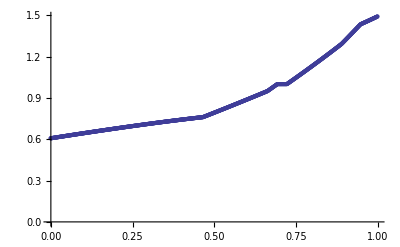

```mathematica
p1=ListPlot[tabT]
```

```mathematica
u1[x_,t_]:=Exp[t+x-1];
```

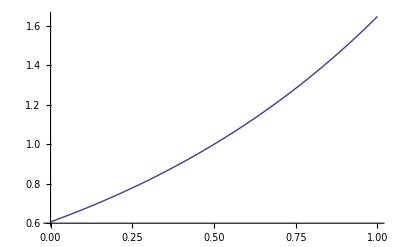

```mathematica
pd1=Plot[u1[x,0.5],{x,0,1}]
```

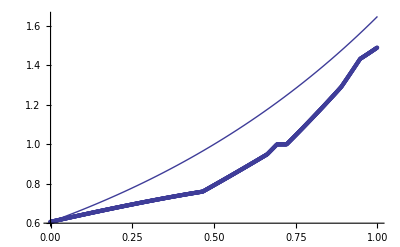

```mathematica
Show[pd1,p1]
```

### alfa = 1/2, t=1

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\agata.chmielowska\Desktop\AlgorytmC- — kopia

```mathematica
str2=OpenRead["temperatury.csv"]
```

InputStream[temperatury.csv,95]

```mathematica
strList2=ReadList[str2]
```

{2.69437,2.69242,2.69048,2.68854,2.6866,2.68466,2.68272,2.68079,2.67886,2.67694,2.67501,2.67309,2.67117,2.66925,2.66734,2.66542,2.66351,2.6616,2.6597,2.65779,2.65589,2.65399,2.6521,2.6502,2.64831,2.64642,2.64453,2.64265,2.64076,2.63888,2.637,2.63513,2.63326,2.63138,2.62952,2.62765,2.62578,2.62392,2.62206,2.62021,2.61835,2.6165,2.61465,2.6128,2.61095,2.60911,2.60727,2.60543,2.60359,2.60176,2.59992,2.59809,2.59627,2.59444,2.59262,2.5908,2.58898,2.58716,2.58535,2.58354,2.58173,2.57992,2.57811,2.57631,2.57451,2.57271,2.57092,2.56912,2.56733,2.56554,2.56375,2.56197,2.56019,2.55841,2.55663,2.55485,2.55308,2.55131,2.54954,2.54777,2.54601,2.54424,2.54248,2.54073,2.53897,2.53722,2.53546,2.53371,2.53197,2.53022,2.52848,2.52674,2.525,2.52327,2.52153,2.5198,2.51807,2.51635,2.51462,2.5129,2.51118,2.50946,2.50775,2.50603,2.50432,2.50261,2.50091,2.4992,2.4975,2.4958,2.4941,2.49241,2.49071,2.48902,2.48733,2.48565,2.48396,2.48228,2.4806,2.47892,2.47725,2.47557,2.4739,2.47223,2.47057,2.4689,2.46724,2.46558,2.46392,2.46227,2.46061,2.45896,2.45731,2.45567,2.45402,2.45238,2.45074,2.4491,2.44747,2.44583,2.4442,2.44257,2.44094,2.43932,2.4377,2.43608,2.43446,2.43284,2.43123,2.42961,2.428,2.4264,2.42479,2.42319,2.42159,2.41999,2.41839,2.4168,2.41521,2.41362,2.41203,2.41044,2.40886,2.40728,2.4057,2.40412,2.40254,2.40097,2.3994,2.39783,2.39627,2.3947,2.39314,2.39158,2.39002,2.38847,2.38691,2.38536,2.38381,2.38226,2.38072,2.37918,2.37764,2.3761,2.37456,2.37303,2.37149,2.36996,2.36844,2.36691,2.36539,2.36387,2.36235,2.36083,2.35931,2.3578,2.35629,2.35478,2.35327,2.35177,2.35027,2.34877,2.34727,2.34577,2.34428,2.34279,2.3413,2.33981,2.33833,2.33684,2.33536,2.33388,2.3324,2.33093,2.32946,2.32799,2.32652,2.32505,2.32359,2.32212,2.32066,2.31921,2.31775,2.3163,2.31484,2.3134,2.31195,2.3105,2.30906,2.30762,2.30618,2.30474,2.30331,2.30187,2.30044,2.29901,2.29759,2.29616,2.29474,2.29332,2.2919,2.29048,2.28907,2.28766,2.28625,2.28484,2.28343,2.28203,2.28063,2.27923,2.27783,2.27644,2.27504,2.27365,2.27226,2.27087,2.26949,2.26811,2.26672,2.26534,2.26397,2.26259,2.26122,2.25985,2.25848,2.25711,2.25575,2.25439,2.25303,2.25167,2.25031,2.24896,2.2476,2.24625,2.24491,2.24356,2.24222,2.24087,2.23953,2.2382,2.23686,2.23553,2.23419,2.23286,2.23154,2.23021,2.22889,2.22756,2.22625,2.22493,2.22361,2.2223,2.22099,2.21968,2.21837,2.21706,2.21576,2.21446,2.21316,2.21186,2.21057,2.20928,2.20798,2.20669,2.20541,2.20412,2.20284,2.20156,2.20028,2.199,2.19773,2.19646,2.19518,2.19392,2.19265,2.19138,2.19012,2.18886,2.1876,2.18635,2.18509,2.18384,2.18259,2.18134,2.1801,2.17885,2.17761,2.17637,2.17513,2.1739,2.17266,2.17143,2.1702,2.16898,2.16775,2.16653,2.16531,2.16409,2.16287,2.16165,2.16044,2.15923,2.15802,2.15681,2.15561,2.1544,2.1532,2.152,2.15081,2.14961,2.14842,2.14723,2.14604,2.14485,2.14367,2.14249,2.14131,2.14013,2.13895,2.13778,2.1366,2.13543,2.13426,2.1331,2.13193,2.13077,2.12961,2.12845,2.1273,2.12614,2.12499,2.12384,2.12269,2.12154,2.1204,2.11926,2.11812,2.11698,2.11584,2.11471,2.11358,2.11245,2.11132,2.11019,2.10907,2.10795,2.10683,2.10571,2.10459,2.10348,2.10237,2.10126,2.10015,2.09904,2.09794,2.09683,2.09573,2.09464,2.09354,2.09245,2.09135,2.09026,2.08918,2.08809,2.08701,2.08592,2.08484,2.08377,2.08269,2.08162,2.08054,2.07947,2.07841,2.07734,2.07628,2.07521,2.07415,2.07309,2.07204,2.07098,2.06993,2.06888,2.06783,2.06679,2.06574,2.0647,2.06366,2.06262,2.06159,2.06055,2.05952,2.05849,2.05746,2.05643,2.05541,2.05439,2.05337,2.05235,2.05133,2.05032,2.04931,2.04829,2.04729,2.04628,2.04528,2.04427,2.04327,2.04227,2.04128,2.04028,2.03929,2.0383,2.03731,2.03632,2.03534,2.03435,2.03337,2.03239,2.03142,2.03044,2.02947,2.0285,2.02753,2.02656,2.0256,2.02463,2.02367,2.02271,2.02176,2.0208,2.01985,2.01889,2.01795,2.017,2.01605,2.01511,2.01417,2.01323,2.01229,2.01135,2.01042,2.00949,2.00856,2.00763,2.0067,2.00578,2.00486,2.00394,2.00302,2.0021,2.00119,2.00028,1.99937,1.99846,1.99755,1.99665,1.99575,1.99484,1.99395,1.99305,1.99216,1.99126,1.99037,1.98948,1.9886,1.98771,1.98683,1.98595,1.98507,1.98419,1.98332,1.98245,1.98158,1.98071,1.97984,1.97898,1.97812,1.97725,1.9764,1.97554,1.97469,1.97383,1.97298,1.97213,1.97129,1.97044,1.9696,1.96876,1.96792,1.96708,1.96625,1.96542,1.96459,1.96376,1.96293,1.96211,1.96128,1.96046,1.95964,1.95883,1.95801,1.9572,1.95639,1.95558,1.95477,1.95397,1.95316,1.95236,1.95156,1.95077,1.94997,1.94918,1.94839,1.9476,1.94681,1.94603,1.94524,1.94446,1.94368,1.94291,1.94213,1.94136,1.94059,1.93982,1.93905,1.93829,1.93752,1.93676,1.936,1.93524,1.93449,1.93374,1.93298,1.93223,1.93149,1.93074,1.93,1.92926,1.92852,1.92778,1.92704,1.92631,1.92558,1.92485,1.92412,1.9234,1.92267,1.92195,1.92123,1.92051,1.9198,1.91908,1.91837,1.91766,1.91695,1.91625,1.91554,1.91484,1.91414,1.91344,1.91275,1.91205,1.91136,1.91067,1.90998,1.9093,1.90861,1.90793,1.90725,1.90657,1.90589,1.90522,1.90455,1.90388,1.90321,1.90254,1.90188,1.90122,1.90056,1.8999,1.89924,1.89859,1.89793,1.89728,1.89663,1.89599,1.89534,1.8947,1.89406,1.89342,1.89278,1.89215,1.89151,1.89088,1.89025,1.88963,1.889,1.88838,1.88776,1.88714,1.88652,1.88591,1.88529,1.88468,1.88407,1.88346,1.88286,1.88226,1.88165,1.88106,1.88046,1.87986,1.87927,1.87868,1.87809,1.8775,1.87691,1.87633,1.87575,1.87517,1.87459,1.87402,1.87344,1.87287,1.8723,1.87173,1.87117,1.8706,1.87004,1.86948,1.86892,1.86837,1.86781,1.86726,1.86671,1.86616,1.86562,1.86507,1.86453,1.86399,1.86345,1.86291,1.86238,1.86185,1.86132,1.86079,1.86026,1.85974,1.85921,1.85869,1.85818,1.85766,1.85714,1.85663,1.85612,1.85561,1.85511,1.8546,1.8541,1.8536,1.8531,1.8526,1.85211,1.85162,1.85113,1.85064,1.85015,1.84967,1.84918,1.8487,1.84823,1.84775,1.84728,1.8468,1.84633,1.84587,1.8454,1.84493,1.84447,1.84401,1.84356,1.8431,1.84265,1.84219,1.84174,1.8413,1.84085,1.84041,1.83997,1.83953,1.83909,1.83865,1.83822,1.83779,1.83736,1.83693,1.83651,1.83608,1.83566,1.83524,1.83483,1.83441,1.834,1.83359,1.83318,1.83277,1.83237,1.83196,1.83156,1.83116,1.83077,1.83037,1.82998,1.82959,1.8292,1.82881,1.82843,1.82805,1.82767,1.82729,1.82691,1.82654,1.82617,1.8258,1.82543,1.82506,1.8247,1.82434,1.82398,1.82362,1.82326,1.82291,1.82256,1.82221,1.82186,1.82152,1.82117,1.82083,1.82049,1.82016,1.81982,1.81949,1.81916,1.81883,1.8185,1.81818,1.81785,1.81753,1.81721,1.8169,1.81658,1.81627,1.81596,1.81565,1.81535,1.81504,1.81474,1.81444,1.81414,1.81385,1.81355,1.81326,1.81297,1.81268,1.8124,1.81211,1.81183,1.81155,1.81128,1.811,1.81073,1.81046,1.81019,1.80992,1.80966,1.80939,1.80913,1.80888,1.80862,1.80836,1.80811,1.80786,1.80761,1.80737,1.80712,1.80688,1.80664,1.8064,1.80617,1.80593,1.8057,1.80547,1.80525,1.80502,1.8048,1.80458,1.80436,1.80414,1.80393,1.80371,1.8035,1.80329,1.80309,1.80288,1.80268,1.80248,1.80228,1.80209,1.80189,1.8017,1.80151,1.80132,1.80114,1.80095,1.80077,1.80059,1.80042,1.80024,1.80007,1.7999,1.79973,1.79956,1.7994,1.79924,1.79908,1.79892,1.79876,1.79861,1.79845,1.7983,1.79816,1.79801,1.79787,1.79773,1.79759,1.79745,1.79732,1.79718,1.79705,1.79692,1.7968,1.79667,1.79655,1.79643,1.79631,1.7962,1.79608,1.79597,1.79586,1.79575,1.79565,1.79554,1.79544,1.79534,1.79525,1.79515,1.79506,1.79497,1.79488,1.79479,1.79471,1.79463,1.79455,1.79447,1.79439,1.79432,1.79425,1.79418,1.79411,1.79405,1.79399,1.79392,1.79387,1.79381,1.79376,1.7937,1.79365,1.79361,1.79356,1.79352,1.79347,1.79344,1.7934,1.79336,1.79333,1.7933,1.79327,1.79324,1.79322,1.7932,1.79318,1.79316,1.79314,1.79313,1.79312,1.79311,1.7931,1.7931,1.7931,1.7931,1.7931,1.7931,1.79311,1.79311,1.79313,1.79314,1.79315,1.79317,1.79319,1.79321,1.79323,1.79326,1.79329,1.79331,1.79335,1.79338,1.79342,1.79346,1.7935,1.79354,1.79358,1.79363,1.79368,1.79373,1.79379,1.79384,1.7939,1.79396,1.79402,1.79409,1.79415,1.79422,1.79429,1.79437,1.79444,1.79452,1.7946,1.79468,1.79477,1.79485,1.79494,1.79503,1.79513,1.79522,1.79532,1.79542,1.79552,1.79563,1.79573,1.79584,1.79595,1.79606,1.79618,1.7963,1.79642,1.79654,1.79666,1.79679,1.79692,1.79705,1.79718}

```mathematica
strList2={2.694366735,2.6924205011,2.6904766452,2.688535165,2.6865960583,2.6846593228,2.6827249562,2.6807929563,2.6788633208,2.6769360474,2.6750111339,2.673088578,2.6711683774,2.6692505299,2.6673350333,2.6654218854,2.6635110837,2.6616026263,2.6596965107,2.6577927348,2.6558912963,2.653992193,2.6520954227,2.6502009832,2.6483088723,2.6464190878,2.6445316277,2.6426464901,2.6407636728,2.6388831739,2.6370049912,2.6351291229,2.6332555669,2.6313843211,2.6295153835,2.6276487522,2.6257844252,2.6239224003,2.6220626757,2.6202052493,2.6183501192,2.6164972832,2.6146467396,2.6127984861,2.610952521,2.6091088421,2.6072674476,2.6054283354,2.6035915035,2.6017569501,2.5999246731,2.5980946705,2.5962669405,2.594441481,2.5926182903,2.5907973667,2.5889787085,2.5871623139,2.5853481813,2.5835363089,2.5817266949,2.5799193378,2.5781142358,2.5763113872,2.5745107902,2.5727124433,2.5709163446,2.5691224926,2.5673308854,2.5655415215,2.5637543992,2.5619695167,2.5601868724,2.5584064646,2.5566282917,2.5548523519,2.5530786436,2.5513071652,2.549537915,2.5477708913,2.5460060924,2.5442435168,2.5424831628,2.5407250286,2.5389691128,2.5372154136,2.5354639293,2.533714707,2.5319677445,2.5302230399,2.5284805912,2.5267403966,2.5250024539,2.5232667613,2.5215333168,2.5198021185,2.5180731643,2.5163464524,2.5146219811,2.512899749,2.5111797548,2.5094619972,2.5077464747,2.5060331861,2.50432213,2.5026133051,2.5009067101,2.4992023436,2.4975002043,2.4958002908,2.4941026019,2.4924071363,2.4907138926,2.4890228697,2.4873340663,2.485647481,2.4839631128,2.4822809603,2.4806010223,2.4789232975,2.4772477847,2.4755744828,2.4739033903,2.4722345062,2.4705678291,2.4689033579,2.4672410913,2.4655810281,2.463923167,2.462267507,2.4606140466,2.4589627849,2.4573137204,2.455666852,2.4540221785,2.4523796988,2.4507394115,2.4491013155,2.4474654096,2.4458316926,2.4442001634,2.4425708206,2.4409436632,2.4393186899,2.4376958995,2.436075291,2.434456863,2.4328406144,2.4312265441,2.4296146509,2.4280049336,2.426397391,2.4247920219,2.4231888253,2.4215877999,2.4199889446,2.4183922582,2.4167977396,2.4152053877,2.4136152011,2.4120271789,2.4104413199,2.408857623,2.4072760869,2.4056967105,2.4041194928,2.4025444326,2.4009715288,2.3994007801,2.3978321856,2.396265744,2.3947014543,2.3931393153,2.391579326,2.3900214851,2.3884657916,2.3869122444,2.3853608424,2.3838115844,2.3822644693,2.3807194962,2.3791766637,2.377635971,2.3760974168,2.3745610001,2.3730267197,2.3714945746,2.3699645638,2.368436686,2.3669109404,2.3653873256,2.3638658408,2.3623464847,2.3608292564,2.3593141548,2.3578011787,2.3562903272,2.3547815992,2.3532749936,2.3517705093,2.3502681453,2.3487679006,2.3472697741,2.3457737647,2.3442798713,2.3427880931,2.3412984288,2.3398108775,2.3383254382,2.3368421097,2.3353608911,2.3338817813,2.3324047793,2.330929884,2.3294570946,2.3279864098,2.3265178287,2.3250513504,2.3235869737,2.3221246976,2.3206645212,2.3192064435,2.3177504633,2.3162965798,2.3148447919,2.3133950987,2.311947499,2.310501992,2.3090585767,2.307617252,2.3061780169,2.3047408705,2.3033058118,2.3018728399,2.3004419536,2.2990131521,2.2975864344,2.2961617995,2.2947392464,2.2933187742,2.2919003819,2.2904840685,2.2890698331,2.2876576748,2.2862475925,2.2848395853,2.2834336522,2.2820297924,2.2806280048,2.2792282885,2.2778306426,2.2764350661,2.2750415581,2.2736501177,2.2722607439,2.2708734357,2.2694881924,2.2681050128,2.2667238962,2.2653448415,2.2639678479,2.2625929145,2.2612200403,2.2598492244,2.2584804659,2.2571137639,2.2557491174,2.2543865257,2.2530259877,2.2516675026,2.2503110695,2.2489566875,2.2476043557,2.2462540732,2.244905839,2.2435596525,2.2422155125,2.2408734183,2.239533369,2.2381953637,2.2368594015,2.2355254817,2.2341936037,2.232863767,2.2315359709,2.2302102148,2.2288864982,2.2275648205,2.2262451811,2.2249275795,2.223612015,2.2222984872,2.2209869954,2.219677539,2.2183701175,2.2170647304,2.2157613771,2.214460057,2.2131607695,2.2118635142,2.2105682904,2.2092750976,2.2079839353,2.206694803,2.2054077,2.2041226258,2.2028395799,2.2015585618,2.2002796118,2.199002729,2.1977279126,2.1964551616,2.1951844753,2.1939158526,2.1926492927,2.1913847949,2.1901223581,2.1888619815,2.1876036643,2.1863474056,2.1850932045,2.1838410602,2.1825909719,2.1813429386,2.1800969596,2.1788530339,2.1776111608,2.1763713393,2.1751335687,2.1738978481,2.1726641768,2.1714325537,2.1702029782,2.1689754493,2.1677499664,2.1665265285,2.1653051348,2.1640857845,2.1628684768,2.161653211,2.1604399863,2.1592288019,2.1580196572,2.1568125513,2.1556074835,2.154404453,2.1532034592,2.1520045012,2.1508075784,2.1496126899,2.1484198351,2.1472290132,2.1460402235,2.1448534652,2.1436687377,2.1424860402,2.141305372,2.1401267324,2.1389501206,2.137775536,2.1366029778,2.1354324453,2.1342639379,2.1330974548,2.1319329953,2.1307705587,2.1296101443,2.1284517515,2.1272953795,2.1261410276,2.1249886952,2.1238383815,2.122690086,2.1215438079,2.1203995465,2.1192573011,2.1181170711,2.1169788559,2.1158426547,2.1147084669,2.1135762918,2.1124461287,2.1113179771,2.1101918362,2.1090677054,2.107945584,2.1068254714,2.1057073669,2.10459127,2.1034771799,2.102365096,2.1012550177,2.1001469444,2.0990408753,2.09793681,2.0968347477,2.0957346878,2.0946366297,2.0935405728,2.0924465165,2.0913544602,2.0902644032,2.0891763449,2.0880902847,2.0870062221,2.0859241564,2.0848440869,2.0837660132,2.0826899346,2.0816158506,2.0805437604,2.0794736636,2.0784055596,2.0773394477,2.0762753274,2.0752131981,2.0741530593,2.0730949103,2.0720387506,2.0709845795,2.0699323967,2.0688822014,2.0678339932,2.0667877713,2.0657435354,2.0647012849,2.0636610191,2.0626227375,2.0615864397,2.060552125,2.0595197929,2.0584894428,2.0574610743,2.0564346867,2.0554102796,2.0543878524,2.0533674046,2.0523489356,2.051332445,2.0503179322,2.0493053967,2.0482948379,2.0472862554,2.0462796487,2.0452750171,2.0442723604,2.0432716778,2.0422729689,2.0412762333,2.0402814704,2.0392886797,2.0382978607,2.037309013,2.036322136,2.0353372292,2.0343542923,2.0333733246,2.0323943258,2.0314172953,2.0304422326,2.0294691374,2.0284980091,2.0275288472,2.0265616513,2.0255964209,2.0246331556,2.0236718549,2.0227125184,2.0217551456,2.020799736,2.0198462892,2.0188948048,2.0179452824,2.0169977221,2.0160521235,2.0151084868,2.0141668117,2.0132270981,2.012289346,2.0113535552,2.0104197257,2.0094878573,2.00855795,2.0076300037,2.0067040182,2.0057799936,2.0048579296,2.0039378263,2.0030196835,2.0021035012,2.0011892793,2.0002770177,1.9993667163,1.9984583752,1.9975519941,1.9966475731,1.995745112,1.9948446508,1.9939461888,1.9930497258,1.9921552614,1.9912627951,1.9903723267,1.9894838556,1.9885973816,1.9877129043,1.9868304232,1.9859499381,1.9850714486,1.9841949542,1.9833204547,1.9824479497,1.9815774387,1.9807089215,1.9798423978,1.9789778671,1.9781153291,1.9772547835,1.9763962299,1.9755396681,1.9746850975,1.973832518,1.9729819292,1.9721333308,1.9712867224,1.9704421037,1.9695994744,1.9687588341,1.9679201827,1.9670835197,1.9662488448,1.9654161577,1.9645854582,1.9637567459,1.9629300205,1.9621052817,1.9612825293,1.960461763,1.9596429824,1.9588261874,1.9580113777,1.9571985529,1.9563877129,1.9555788574,1.954771986,1.9539670987,1.9531641951,1.9523632749,1.9515643379,1.9507673839,1.9499724127,1.9491794239,1.9483884174,1.9475993929,1.9468123501,1.946027289,1.9452442091,1.9444631104,1.9436839925,1.9429068553,1.9421316985,1.941358522,1.9405873255,1.9398181088,1.9390508717,1.938285614,1.9375223355,1.936761036,1.9360017153,1.9352443732,1.9344890095,1.933735624,1.9329842166,1.932234787,1.9314873351,1.9307418607,1.9299983636,1.9292568437,1.9285173007,1.9277797345,1.927044145,1.9263105319,1.9255788952,1.9248492346,1.92412155,1.9233958412,1.9226721082,1.9219503507,1.9212305686,1.9205127617,1.91979693,1.9190830732,1.9183711913,1.9176612841,1.9169533514,1.9162473933,1.9155434094,1.9148413997,1.9141413642,1.9134433025,1.9127472148,1.9120531007,1.9113609603,1.9106707934,1.9099826,1.9092963798,1.9086121328,1.907929859,1.9072495582,1.9065712303,1.9058948752,1.9052204929,1.9045480832,1.9038776461,1.9032091816,1.9025426894,1.9018781696,1.9012156221,1.9005550468,1.8998964436,1.8992398125,1.8985851534,1.8979324663,1.8972817511,1.8966330077,1.8959862361,1.8953414363,1.8946986081,1.8940577517,1.8934188668,1.8927819535,1.8921470118,1.8915140415,1.8908830428,1.8902540155,1.8896269596,1.8890018751,1.888378762,1.8877576202,1.8871384498,1.8865212508,1.885906023,1.8852927666,1.8846814815,1.8840721676,1.8834648251,1.8828594539,1.882256054,1.8816546255,1.8810551682,1.8804576823,1.8798621678,1.8792686247,1.8786770529,1.8780874526,1.8774998237,1.8769141663,1.8763304804,1.8757487661,1.8751690233,1.8745912521,1.8740154526,1.8734416248,1.8728697688,1.8722998845,1.8717319721,1.8711660316,1.8706020631,1.8700400666,1.8694800421,1.8689219898,1.8683659098,1.8678118022,1.8672596677,1.8667095067,1.8661613197,1.8656151073,1.86507087,1.8645286082,1.8639883226,1.8634500136,1.8629136818,1.8623793276,1.8618469516,1.8613165544,1.8607881365,1.8602616984,1.8597372406,1.8592147637,1.8586942682,1.8581757546,1.8576592236,1.8571446757,1.8566321113,1.8561215311,1.8556129356,1.8551063254,1.854601701,1.854099063,1.853598455,1.8530998772,1.85260333,1.8521088137,1.8516163286,1.8511258749,1.850637453,1.8501510631,1.8496667056,1.8491843808,1.848704089,1.8482258305,1.8477496056,1.8472754146,1.8468032579,1.8463331358,1.8458650485,1.8453989966,1.8449349802,1.8444729997,1.8440130554,1.8435551477,1.8430992769,1.8426454434,1.8421936475,1.8417438896,1.84129617,1.840850489,1.8404068471,1.8399652446,1.8395256818,1.8390881591,1.8386526768,1.8382192355,1.8377878353,1.8373584767,1.8369311601,1.8365058859,1.8360826543,1.8356614658,1.8352423207,1.8348252192,1.8344101618,1.8339971487,1.8335861802,1.8331772568,1.8327703787,1.8323655463,1.8319627599,1.8315620199,1.8311633266,1.8307666803,1.8303720815,1.8299795304,1.8295890275,1.8292005731,1.8288141675,1.8284298111,1.8280475043,1.8276672474,1.8272890409,1.8269128851,1.8265387803,1.826166727,1.8257967256,1.8254287763,1.8250628797,1.8246990361,1.8243372459,1.8239775095,1.8236198273,1.8232641996,1.822910627,1.8225591097,1.8222096483,1.8218622431,1.8215168945,1.821173603,1.820832369,1.8204931928,1.820156075,1.8198210159,1.8194880159,1.8191570756,1.8188281953,1.8185013755,1.8181766166,1.817853919,1.8175332833,1.8172147098,1.816898199,1.8165837513,1.8162713673,1.8159610473,1.8156527918,1.8153466013,1.8150424762,1.8147404171,1.8144404243,1.8141424984,1.8138466399,1.8135528491,1.8132611267,1.812971473,1.8126838885,1.8123983738,1.8121149294,1.8118335556,1.8115542531,1.8112770223,1.8110018638,1.8107287779,1.8104577653,1.8101888265,1.8099219619,1.809657172,1.8093944574,1.8091338187,1.8088752562,1.8086187706,1.8083643624,1.808112032,1.8078617801,1.8076136072,1.8073675137,1.8071235003,1.8068815674,1.8066417157,1.8064039457,1.8061682579,1.8059346528,1.8057031311,1.8054736932,1.8052463398,1.8050210714,1.8047978885,1.8045767918,1.8043577818,1.8041408591,1.8039260242,1.8037132777,1.8035026203,1.8032940524,1.8030875747,1.8028831877,1.8026808922,1.8024806885,1.8022825774,1.8020865594,1.8018926352,1.8017008052,1.8015110703,1.8013234309,1.8011378876,1.8009544411,1.800773092,1.8005938409,1.8004166884,1.8002416352,1.8000686818,1.7998978289,1.7997290772,1.7995624272,1.7993978796,1.7992354351,1.7990750943,1.7989168577,1.7987607261,1.7986067002,1.7984547805,1.7983049677,1.7981572625,1.7980116655,1.7978681775,1.797726799,1.7975875307,1.7974503732,1.7973153274,1.7971823938,1.7970515731,1.796922866,1.7967962732,1.7966717953,1.796549433,1.7964291871,1.7963110583,1.7961950471,1.7960811543,1.7959693807,1.7958597268,1.7957521935,1.7956467814,1.7955434913,1.7954423238,1.7953432796,1.7952463595,1.7951515642,1.7950588944,1.7949683509,1.7948799343,1.7947936455,1.794709485,1.7946274538,1.7945475524,1.7944697816,1.7943941423,1.794320635,1.7942492607,1.79418002,1.7941129136,1.7940479424,1.793985107,1.7939244083,1.7938658471,1.793809424,1.7937551398,1.7937029953,1.7936529914,1.7936051287,1.793559408,1.7935158301,1.7934743959,1.793435106,1.7933979613,1.7933629626,1.7933301107,1.7932994062,1.7932708502,1.7932444433,1.7932201863,1.7931980801,1.7931781255,1.7931603232,1.7931446742,1.7931311791,1.7931198389,1.7931106543,1.7931036262,1.7930987553,1.7930960427,1.7930954889,1.793097095,1.7931008616,1.7931067898,1.7931148802,1.7931251338,1.7931375514,1.7931521338,1.7931688819,1.7931877966,1.7932088786,1.793232129,1.7932575484,1.7932851379,1.7933148982,1.7933468302,1.7933809348,1.7934172129,1.7934556653,1.793496293,1.7935390968,1.7935840775,1.7936312361,1.7936805735,1.7937320906,1.7937857882,1.7938416673,1.7938997287,1.7939599734,1.7940224022,1.7940870161,1.794153816,1.7942228027,1.7942939772,1.7943673405,1.7944428934,1.7945206375,1.7946005751,1.7946827089,1.7947670412,1.7948535746,1.7949423114,1.7950332542,1.7951264054,1.7952217675,1.795319343,1.7954191342,1.7955211438,1.795625374,1.7957318275,1.7958405065,1.7959514137,1.7960645515,1.7961799222,1.7962975284,1.7964173725,1.796539457,1.7966637843,1.7967903569,1.7969191771,1.7970502476,1.7971835706};
```

```mathematica
tabT2=Table[{1-i*0.001,strList2[[i]]},{i,1,1001}];
```

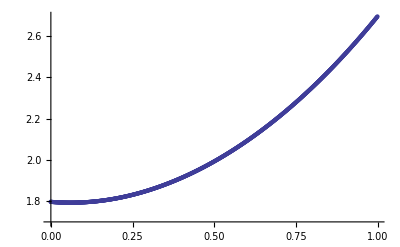

```mathematica
p2=ListPlot[tabT2]
```

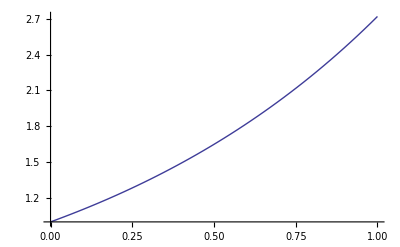

```mathematica
pd2=Plot[u1[x,1],{x,0,1}]
```

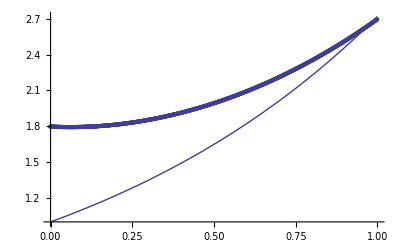

```mathematica
Show[pd2,p2]
```

### alfa = 8/10, t=1/2

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\agata.chmielowska\Desktop\AlgorytmC- — kopia

```mathematica
str3=OpenRead["temperatury.csv"]
```

InputStream[temperatury.csv,96]

```mathematica
strList3=ReadList[str3]
```

{1.56152,1.55997,1.55842,1.55688,1.55533,1.55379,1.55225,1.55071,1.54917,1.54763,1.5461,1.54456,1.54303,1.5415,1.53997,1.53845,1.53692,1.5354,1.53387,1.53235,1.53084,1.52932,1.5278,1.52629,1.52478,1.52327,1.52176,1.52025,1.51875,1.51725,1.51574,1.51425,1.51275,1.51125,1.50976,1.50827,1.50678,1.50529,1.50381,1.50232,1.50084,1.49936,1.49788,1.49641,1.49494,1.49346,1.492,1.49053,1.48906,1.4876,1.48614,1.48468,1.48322,1.48177,1.48032,1.47887,1.47742,1.47597,1.47453,1.47309,1.47165,1.47021,1.46878,1.46735,1.46592,1.46449,1.46306,1.46164,1.46022,1.4588,1.45738,1.45597,1.45456,1.45315,1.45174,1.45034,1.44893,1.44753,1.44613,1.44474,1.44334,1.44195,1.44056,1.43917,1.43779,1.43641,1.43502,1.43365,1.43227,1.4309,1.42953,1.42816,1.42679,1.42543,1.42406,1.4227,1.42135,1.41999,1.41864,1.41729,1.41594,1.41459,1.41325,1.41191,1.41057,1.40923,1.4079,1.40656,1.40523,1.40391,1.40258,1.40126,1.39994,1.39862,1.3973,1.39599,1.39468,1.39337,1.39206,1.39076,1.38946,1.38816,1.38686,1.38556,1.38427,1.38298,1.38169,1.38041,1.37913,1.37785,1.37657,1.37529,1.37402,1.37275,1.37148,1.37021,1.36895,1.36769,1.36643,1.36517,1.36392,1.36267,1.36142,1.36017,1.35892,1.35768,1.35644,1.35521,1.35397,1.35274,1.35151,1.34878,1.34561,1.34245,1.33928,1.33613,1.33297,1.32982,1.32667,1.32353,1.32039,1.31725,1.31411,1.31172,1.30938,1.30704,1.30471,1.30238,1.30005,1.29772,1.2954,1.29308,1.29076,1.28845,1.28613,1.28382,1.28152,1.27921,1.27691,1.27461,1.27231,1.27001,1.26772,1.26543,1.26314,1.26085,1.25857,1.25629,1.25401,1.25173,1.24946,1.24719,1.24492,1.24265,1.24039,1.23812,1.23586,1.23361,1.23135,1.2291,1.22684,1.2246,1.22235,1.22011,1.21786,1.21562,1.21339,1.21115,1.20892,1.20669,1.20446,1.20223,1.20001,1.19778,1.19556,1.19334,1.19113,1.18891,1.1867,1.18449,1.18229,1.18008,1.17788,1.17568,1.17348,1.17128,1.16908,1.16689,1.1647,1.16251,1.16032,1.15814,1.15595,1.15377,1.15159,1.14942,1.14724,1.14507,1.1429,1.14073,1.13856,1.1364,1.13423,1.13207,1.12991,1.12775,1.1256,1.12344,1.12129,1.11914,1.11699,1.11484,1.1127,1.11056,1.10841,1.10627,1.10414,1.102,1.09987,1.09773,1.0956,1.09347,1.09135,1.08922,1.0871,1.08498,1.08286,1.08074,1.07862,1.07651,1.07439,1.07228,1.07017,1.06806,1.06595,1.06385,1.06175,1.05964,1.05754,1.05544,1.05335,1.05125,1.04916,1.04707,1.04497,1.04288,1.0408,1.03871,1.03663,1.03454,1.03246,1.03038,1.0283,1.02623,1.02415,1.02208,1.02,1.01793,1.01586,1.01379,1.01173,1.00966,1.0076,1.00553,1.00347,1.00141,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.999229,0.997999,0.996771,0.995542,0.994314,0.993086,0.991859,0.990632,0.989405,0.988179,0.986953,0.985728,0.984502,0.983278,0.982053,0.980829,0.979605,0.978382,0.977159,0.975936,0.974714,0.973491,0.97227,0.971048,0.969827,0.968607,0.967386,0.966166,0.964946,0.963727,0.962508,0.961289,0.960071,0.958852,0.957635,0.956417,0.9552,0.953983,0.952767,0.95155,0.950334,0.949119,0.947903,0.946688,0.945473,0.944259,0.943045,0.941831,0.940617,0.939404,0.938191,0.936978,0.935766,0.934554,0.933342,0.93213,0.930919,0.929708,0.928497,0.927286,0.926076,0.924866,0.923656,0.922447,0.921238,0.920029,0.91882,0.917612,0.916403,0.915195,0.913988,0.91278,0.911573,0.910366,0.909159,0.907953,0.906747,0.905541,0.904335,0.903129,0.901924,0.900719,0.899514,0.898309,0.897105,0.8959,0.894696,0.893493,0.892289,0.891086,0.889882,0.888679,0.887476,0.886274,0.885071,0.883869,0.882667,0.881465,0.880264,0.879062,0.877861,0.87666,0.875459,0.874258,0.873058,0.871857,0.870657,0.869457,0.868257,0.867058,0.865858,0.864659,0.863459,0.86226,0.861061,0.859863,0.858664,0.857466,0.856267,0.855069,0.853871,0.852673,0.851475,0.850278,0.84908,0.847883,0.846685,0.845488,0.844291,0.843094,0.841898,0.840701,0.839753,0.839435,0.839117,0.838797,0.838476,0.838155,0.837833,0.83751,0.837186,0.836861,0.836535,0.836209,0.835882,0.835554,0.835225,0.834895,0.834565,0.834234,0.833902,0.833569,0.833235,0.832901,0.832566,0.83223,0.831893,0.831555,0.831217,0.830878,0.830538,0.830198,0.829856,0.829514,0.829171,0.828828,0.828484,0.828138,0.827793,0.827446,0.827099,0.826751,0.826402,0.826053,0.825703,0.825352,0.825,0.824648,0.824295,0.823941,0.823587,0.823232,0.822876,0.82252,0.822163,0.821805,0.821446,0.821087,0.820727,0.820367,0.820006,0.819644,0.819282,0.818918,0.818555,0.81819,0.817825,0.817459,0.817093,0.816726,0.816358,0.81599,0.815621,0.815252,0.814881,0.814511,0.814139,0.813767,0.813394,0.813021,0.812647,0.812273,0.811898,0.811522,0.811146,0.810769,0.810392,0.810014,0.809635,0.809256,0.808876,0.808496,0.808115,0.807733,0.807351,0.806968,0.806585,0.806201,0.805817,0.805432,0.805047,0.804661,0.804274,0.803887,0.8035,0.803111,0.802723,0.802333,0.801944,0.801553,0.801163,0.800771,0.800379,0.799987,0.799594,0.799201,0.798807,0.798412,0.798017,0.797622,0.797226,0.796829,0.796432,0.796035,0.795637,0.795239,0.79484,0.79444,0.79404,0.79364,0.793239,0.792838,0.792436,0.792034,0.791631,0.791228,0.790824,0.79042,0.790015,0.78961,0.789205,0.788799,0.788392,0.787985,0.787578,0.78717,0.786762,0.786353,0.785944,0.785535,0.785125,0.784714,0.784304,0.783892,0.783481,0.783069,0.782656,0.782243,0.78183,0.781416,0.781002,0.780587,0.780172,0.779757,0.779341,0.778925,0.778508,0.778091,0.777674,0.777256,0.776838,0.776419,0.776,0.775581,0.775161,0.774741,0.774321,0.7739,0.773478,0.773057,0.772635,0.772212,0.77179,0.771367,0.770943,0.770519,0.770095,0.769671,0.769246,0.76882,0.768395,0.767969,0.767542,0.767116,0.766689,0.766261,0.765834,0.765406,0.764977,0.764549,0.764119,0.76369,0.76326,0.76283,0.7624,0.761969,0.761538,0.761107,0.760675,0.760243,0.759811,0.759378,0.758945,0.758512,0.758078,0.757644,0.75721,0.756776,0.756341,0.755906,0.75547,0.755035,0.754599,0.754162,0.753726,0.753289,0.752852,0.752414,0.751976,0.751538,0.7511,0.750661,0.750222,0.749783,0.749344,0.748904,0.748464,0.748023,0.747583,0.747142,0.746701,0.746259,0.745818,0.745376,0.744934,0.744491,0.744048,0.743605,0.743162,0.742719,0.742275,0.741831,0.741387,0.740942,0.740497,0.740052,0.739607,0.739161,0.738716,0.738269,0.737823,0.737377,0.73693,0.736483,0.736036,0.735588,0.735141,0.734693,0.734244,0.733796,0.733347,0.732898,0.732449,0.732,0.731551,0.731101,0.730651,0.730201,0.72975,0.729299,0.728849,0.728397,0.727946,0.727495,0.727043,0.726591,0.726139,0.725686,0.725234,0.724781,0.724328,0.723875,0.723421,0.722968,0.722514,0.72206,0.721606,0.721151,0.720697,0.720242,0.719787,0.719332,0.718876,0.718421,0.717965,0.717509,0.717053,0.716596,0.71614,0.715683,0.715226,0.714769,0.714312,0.713854,0.713397,0.712939,0.712481,0.712022,0.711564,0.711106,0.710647,0.710188,0.709729,0.70927,0.70881,0.708351,0.707891,0.707431,0.706971,0.70651,0.70605,0.705589,0.705129,0.704668,0.704207,0.703745,0.703284,0.702822,0.702361,0.701899,0.701437,0.700974,0.700512,0.700049,0.699587,0.699124,0.698661,0.698198,0.697734,0.697271,0.696807,0.696344,0.69588,0.695416,0.694951,0.694487,0.694022,0.693558,0.693093,0.692628,0.692163,0.691698,0.691232,0.690767,0.690301,0.689835,0.689369,0.688903,0.688437,0.687971,0.687504,0.687038,0.686571,0.686104,0.685637,0.68517,0.684702,0.684235,0.683767,0.6833,0.682832,0.682364,0.681896,0.681428,0.680959,0.680491,0.680022,0.679553,0.679084,0.678616,0.678146,0.677677,0.677208,0.676738,0.676269,0.675799,0.675329,0.674859,0.674389,0.673919,0.673448,0.672978,0.672507,0.672037,0.671566,0.671095,0.670624,0.670153,0.669681,0.66921,0.668738,0.668267,0.667795,0.667323,0.666851,0.666379,0.665907,0.665434,0.664962,0.664489,0.664017,0.663544,0.663071,0.662598,0.662125,0.661651,0.661178,0.660705,0.660231,0.659757,0.659284,0.65881,0.658336,0.657861,0.657387,0.656913,0.656438,0.655964,0.655489,0.655014,0.65454,0.654065,0.65359,0.653114,0.652639,0.652164,0.651688,0.651212,0.650737,0.650261,0.649785,0.649309,0.648833,0.648357,0.64788,0.647404,0.646927,0.64645,0.645974,0.645497,0.64502,0.644543,0.644066,0.643588,0.643111,0.642633,0.642156,0.641678,0.6412,0.640722,0.640244,0.639766,0.639288,0.63881,0.638331,0.637853,0.637374,0.636896,0.636417,0.635938,0.635459,0.63498,0.634501,0.634021,0.633542,0.633062,0.632583,0.632103,0.631623,0.631143,0.630663,0.630183,0.629703,0.629222,0.628742,0.628262,0.627781,0.6273,0.626819,0.626338,0.625857,0.625376,0.624895,0.624414,0.623932,0.623451,0.622969,0.622487,0.622005,0.621523,0.621041,0.620559,0.620077,0.619594,0.619112,0.618629,0.618147,0.617664,0.617181,0.616698,0.616215,0.615732,0.615248,0.614765,0.614281,0.613798,0.613314,0.61283,0.612346,0.611862,0.611378,0.610894,0.610409,0.609925,0.60944,0.608956,0.608471,0.607986,0.607501,0.607016,0.606531}

```mathematica
strList3={1.5615206822,1.5599708836,1.5584227328,1.5568762269,1.5553313628,1.5537881376,1.5522465482,1.5507065918,1.5491682653,1.5476315656,1.5460964899,1.5445630352,1.5430311983,1.5415009763,1.5399723702,1.5384453926,1.5369200557,1.5353963723,1.5338743546,1.5323540151,1.5308353663,1.5293184206,1.5278031904,1.5262896881,1.5247779261,1.5232679168,1.5217596726,1.5202532059,1.518748529,1.5172456543,1.5157446724,1.5142455948,1.5127484327,1.5112531974,1.5097599002,1.5082685524,1.5067791653,1.5052917503,1.5038063185,1.5023228813,1.5008414498,1.4993620355,1.4978846496,1.4964093033,1.4949360078,1.4934647746,1.4919956146,1.4905285394,1.48906356,1.4876006877,1.4861399338,1.4846813095,1.4832248261,1.4817704947,1.4803183266,1.4788683331,1.4774205254,1.4759749146,1.4745315121,1.4730903291,1.4716513693,1.4702146346,1.4687801268,1.4673478477,1.465917799,1.4644899827,1.4630644006,1.4616410545,1.4602199462,1.4588010776,1.4573844505,1.4559700669,1.4545579285,1.4531480374,1.4517403953,1.4503350041,1.4489318658,1.4475309823,1.4461323554,1.4447359871,1.4433418794,1.4419500341,1.4405604532,1.4391731387,1.4377880925,1.4364053166,1.435024813,1.4336465836,1.4322706304,1.4308969555,1.4295255608,1.4281564483,1.4267896203,1.4254250791,1.4240628271,1.4227028667,1.4213452004,1.4199898306,1.4186367596,1.41728599,1.4159375242,1.4145913646,1.4132475136,1.4119059739,1.4105667477,1.4092298377,1.4078952462,1.4065629759,1.4052330292,1.4039054086,1.4025801166,1.4012571558,1.3999365287,1.3986182379,1.3973022859,1.3959886753,1.3946774087,1.3933684885,1.3920619176,1.3907576983,1.3894558334,1.3881563255,1.3868591771,1.385564391,1.3842719697,1.3829819159,1.3816942323,1.3804089216,1.3791259864,1.3778454294,1.3765672533,1.3752914609,1.3740180548,1.3727470378,1.3714784126,1.370212182,1.3689483487,1.3676869155,1.3664278851,1.3651712604,1.3639170442,1.3626652392,1.3614158483,1.3601688743,1.35892432,1.3576821884,1.3564424821,1.3552052042,1.3539703575,1.3527379449,1.3515079692,1.3487792068,1.3456110509,1.3424462853,1.3392848949,1.3361268644,1.3329721789,1.3298208231,1.326672782,1.3235280405,1.3203865836,1.3172483962,1.3141134634,1.3117154418,1.3093770923,1.3070413231,1.3047081253,1.3023774897,1.3000494075,1.2977238695,1.2954008667,1.2930803902,1.290762431,1.2884469802,1.2861340287,1.2838235676,1.281515588,1.279210081,1.2769070377,1.2746064472,1.2723083007,1.2700125893,1.2677193041,1.2654284361,1.2631399765,1.2608539164,1.258570247,1.2562889594,1.2540100448,1.2517334943,1.2494592991,1.2471874505,1.2449179396,1.2426507577,1.2403858959,1.2381233455,1.2358630978,1.233605144,1.2313494754,1.2290960831,1.2268449587,1.2245960932,1.2223494781,1.2201051046,1.2178629641,1.2156230478,1.2133853472,1.2111498536,1.2089165584,1.2066854528,1.2044565284,1.2022297765,1.2000051884,1.1977827557,1.1955624696,1.1933443217,1.1911283034,1.1889144061,1.1867026212,1.1844929403,1.1822853548,1.1800798562,1.177876436,1.1756750856,1.1734757966,1.1712785604,1.1690833687,1.1668902129,1.1646990846,1.1625099753,1.1603228766,1.15813778,1.1559546772,1.1537735596,1.1515944189,1.1494172467,1.1472420345,1.1450687741,1.142897457,1.1407280748,1.1385606191,1.1363950817,1.1342314542,1.1320697281,1.1299098953,1.1277519473,1.1255958759,1.1234416727,1.1212893294,1.1191388377,1.1169901894,1.1148433761,1.1126983896,1.1105552216,1.1084138638,1.1062743081,1.1041365461,1.1020005695,1.0998663703,1.09773394,1.0956032706,1.0934743538,1.0913471814,1.0892217452,1.0870980369,1.0849760485,1.0828557717,1.0807371984,1.0786203203,1.0765051293,1.0743916173,1.0722797761,1.0701695976,1.0680610736,1.065954196,1.0638489567,1.0617453475,1.0596433603,1.057542987,1.0554442196,1.0533470499,1.0512514698,1.0491574712,1.0470650461,1.0449741864,1.042884884,1.0407971308,1.0387109188,1.03662624,1.0345430862,1.0324614495,1.0303813217,1.0283026949,1.0262255611,1.0241499122,1.0220757401,1.020003037,1.0179317947,1.0158620053,1.0137936607,1.011726753,1.0096612742,1.0075972163,1.0055345713,1.0034733312,1.0014134881,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0.9992285992,0.9979994022,0.9967705781,0.9955421251,0.9943140415,0.9930863256,0.9918589757,0.9906319901,0.989405367,0.9881791047,0.9869532015,0.9857276556,0.9845024653,0.9832776289,0.9820531445,0.9808290105,0.9796052251,0.9783817864,0.9771586928,0.9759359424,0.9747135335,0.9734914642,0.9722697329,0.9710483377,0.9698272768,0.9686065484,0.9673861506,0.9661660818,0.96494634,0.9637269235,0.9625078304,0.9612890588,0.9600706071,0.9588524732,0.9576346554,0.9564171518,0.9551999606,0.9539830799,0.9527665079,0.9515502426,0.9503342823,0.949118625,0.9479032688,0.9466882119,0.9454734524,0.9442589884,0.9430448179,0.9418309391,0.9406173502,0.939404049,0.9381910338,0.9369783027,0.9357658536,0.9345536847,0.933341794,0.9321301796,0.9309188395,0.9297077718,0.9284969745,0.9272864458,0.9260761835,0.9248661857,0.9236564506,0.922446976,0.92123776,0.9200288006,0.9188200958,0.9176116437,0.9164034422,0.9151954893,0.913987783,0.9127803212,0.9115731021,0.9103661234,0.9091593833,0.9079528797,0.9067466104,0.9055405735,0.904334767,0.9031291888,0.9019238367,0.9007187088,0.899513803,0.8983091171,0.8971046492,0.8959003971,0.8946963588,0.8934925321,0.892288915,0.8910855053,0.889882301,0.8886792998,0.8874764998,0.8862738988,0.8850714946,0.8838692851,0.8826672682,0.8814654417,0.8802638035,0.8790623514,0.8778610833,0.876659997,0.8754590903,0.8742583611,0.8730578071,0.8718574262,0.8706572163,0.869457175,0.8682573003,0.8670575899,0.8658580415,0.864658653,0.8634594222,0.8622603468,0.8610614246,0.8598626534,0.8586640309,0.8574655549,0.856267223,0.8550690332,0.8538709831,0.8526730704,0.8514752928,0.8502776482,0.8490801341,0.8478827484,0.8466854887,0.8454883527,0.8442913382,0.8430944427,0.841897664,0.8407009999,0.8397534252,0.8394354106,0.8391165425,0.8387968246,0.8384762606,0.838154854,0.8378326085,0.8375095278,0.8371856154,0.836860875,0.8365353101,0.8362089242,0.835881721,0.835553704,0.8352248767,0.8348952426,0.8345648053,0.8342335682,0.8339015349,0.8335687087,0.8332350932,0.8329006919,0.8325655081,0.8322295452,0.8318928068,0.8315552962,0.8312170167,0.8308779719,0.830538165,0.8301975993,0.8298562783,0.8295142053,0.8291713836,0.8288278165,0.8284835074,0.8281384594,0.8277926759,0.8274461601,0.8270989154,0.8267509449,0.8264022519,0.8260528395,0.8257027111,0.8253518698,0.8250003188,0.8246480613,0.8242951004,0.8239414393,0.8235870811,0.8232320291,0.8228762862,0.8225198556,0.8221627404,0.8218049438,0.8214464687,0.8210873182,0.8207274955,0.8203670035,0.8200058453,0.8196440239,0.8192815423,0.8189184035,0.8185546106,0.8181901665,0.8178250741,0.8174593365,0.8170929566,0.8167259373,0.8163582816,0.8159899923,0.8156210725,0.8152515249,0.8148813525,0.8145105582,0.8141391448,0.8137671152,0.8133944722,0.8130212186,0.8126473574,0.8122728913,0.8118978231,0.8115221556,0.8111458917,0.810769034,0.8103915853,0.8100135485,0.8096349262,0.8092557211,0.8088759361,0.8084955739,0.808114637,0.8077331283,0.8073510505,0.8069684061,0.8065851979,0.8062014285,0.8058171005,0.8054322167,0.8050467796,0.8046607919,0.8042742562,0.803887175,0.8034995509,0.8031113866,0.8027226846,0.8023334475,0.8019436778,0.801553378,0.8011625507,0.8007711985,0.8003793237,0.799986929,0.7995940169,0.7992005897,0.7988066501,0.7984122003,0.7980172431,0.7976217806,0.7972258155,0.7968293501,0.7964323868,0.7960349281,0.7956369764,0.795238534,0.7948396034,0.7944401868,0.7940402868,0.7936399056,0.7932390455,0.792837709,0.7924358984,0.7920336159,0.7916308639,0.7912276446,0.7908239605,0.7904198137,0.7900152066,0.7896101413,0.7892046202,0.7887986456,0.7883922196,0.7879853444,0.7875780224,0.7871702557,0.7867620465,0.786353397,0.7859443095,0.785534786,0.7851248288,0.78471444,0.7843036218,0.7838923763,0.7834807056,0.783068612,0.7826560974,0.7822431641,0.781829814,0.7814160494,0.7810018722,0.7805872847,0.7801722887,0.7797568865,0.77934108,0.7789248713,0.7785082624,0.7780912554,0.7776738522,0.7772560549,0.7768378655,0.776419286,0.7760003183,0.7755809645,0.7751612264,0.7747411062,0.7743206056,0.7738997267,0.7734784714,0.7730568416,0.7726348393,0.7722124663,0.7717897246,0.771366616,0.7709431425,0.7705193059,0.7700951081,0.7696705509,0.7692456363,0.768820366,0.7683947419,0.7679687659,0.7675424397,0.7671157652,0.7666887441,0.7662613783,0.7658336696,0.7654056198,0.7649772306,0.7645485038,0.7641194411,0.7636900444,0.7632603153,0.7628302557,0.7623998672,0.7619691515,0.7615381104,0.7611067456,0.7606750587,0.7602430515,0.7598107257,0.7593780829,0.7589451248,0.7585118531,0.7580782694,0.7576443754,0.7572101726,0.7567756628,0.7563408476,0.7559057285,0.7554703073,0.7550345854,0.7545985645,0.7541622462,0.753725632,0.7532887236,0.7528515224,0.7524140301,0.7519762482,0.7515381783,0.7510998218,0.7506611803,0.7502222554,0.7497830485,0.7493435611,0.7489037948,0.7484637511,0.7480234314,0.7475828372,0.7471419699,0.7467008311,0.7462594222,0.7458177447,0.7453757999,0.7449335894,0.7444911145,0.7440483768,0.7436053775,0.7431621181,0.7427186,0.7422748246,0.7418307932,0.7413865074,0.7409419683,0.7404971775,0.7400521362,0.7396068458,0.7391613077,0.7387155231,0.7382694935,0.7378232201,0.7373767043,0.7369299473,0.7364829506,0.7360357153,0.7355882427,0.7351405342,0.734692591,0.7342444144,0.7337960057,0.733347366,0.7328984968,0.7324493991,0.7320000742,0.7315505234,0.7311007479,0.7306507489,0.7302005277,0.7297500853,0.729299423,0.728848542,0.7283974436,0.7279461287,0.7274945987,0.7270428547,0.7265908978,0.7261387292,0.7256863501,0.7252337615,0.7247809646,0.7243279606,0.7238747505,0.7234213354,0.7229677165,0.7225138949,0.7220598716,0.7216056477,0.7211512243,0.7206966025,0.7202417834,0.719786768,0.7193315573,0.7188761524,0.7184205544,0.7179647642,0.717508783,0.7170526117,0.7165962513,0.7161397028,0.7156829673,0.7152260458,0.7147689391,0.7143116484,0.7138541746,0.7133965186,0.7129386815,0.7124806642,0.7120224676,0.7115640926,0.7111055403,0.7106468116,0.7101879073,0.7097288284,0.7092695758,0.7088101505,0.7083505533,0.7078907851,0.7074308468,0.7069707393,0.7065104635,0.7060500203,0.7055894104,0.7051286348,0.7046676944,0.7042065899,0.7037453222,0.7032838922,0.7028223006,0.7023605484,0.7018986362,0.701436565,0.7009743356,0.7005119486,0.700049405,0.6995867055,0.6991238509,0.6986608419,0.6981976794,0.6977343641,0.6972708968,0.6968072782,0.696343509,0.69587959,0.695415522,0.6949513056,0.6944869416,0.6940224307,0.6935577735,0.693092971,0.6926280236,0.6921629321,0.6916976972,0.6912323196,0.6907667999,0.6903011388,0.689835337,0.6893693952,0.6889033139,0.6884370939,0.6879707358,0.6875042401,0.6870376076,0.6865708389,0.6861039345,0.6856368952,0.6851697214,0.6847024139,0.6842349731,0.6837673997,0.6832996943,0.6828318574,0.6823638897,0.6818957916,0.6814275637,0.6809592067,0.680490721,0.6800221072,0.6795533658,0.6790844974,0.6786155025,0.6781463816,0.6776771352,0.6772077638,0.676738268,0.6762686482,0.6757989049,0.6753290387,0.6748590499,0.6743889391,0.6739187068,0.6734483534,0.6729778794,0.6725072851,0.6720365712,0.6715657379,0.6710947859,0.6706237154,0.6701525269,0.6696812208,0.6692097976,0.6687382577,0.6682666014,0.6677948292,0.6673229414,0.6668509385,0.6663788208,0.6659065887,0.6654342426,0.6649617828,0.6644892097,0.6640165237,0.6635437251,0.6630708142,0.6625977914,0.6621246571,0.6616514115,0.661178055,0.6607045878,0.6602310104,0.6597573229,0.6592835258,0.6588096193,0.6583356037,0.6578614793,0.6573872463,0.656912905,0.6564384558,0.6559638988,0.6554892344,0.6550144627,0.6545395841,0.6540645987,0.6535895068,0.6531143087,0.6526390045,0.6521635945,0.6516880789,0.6512124579,0.6507367317,0.6502609006,0.6497849646,0.649308924,0.6488327791,0.6483565298,0.6478801765,0.6474037193,0.6469271584,0.6464504938,0.6459737259,0.6454968546,0.6450198802,0.6445428028,0.6440656225,0.6435883395,0.6431109538,0.6426334656,0.642155875,0.6416781822,0.6412003871,0.6407224898,0.6402444906,0.6397663895,0.6392881864,0.6388098816,0.6383314751,0.6378529669,0.6373743571,0.6368956458,0.636416833,0.6359379187,0.635458903,0.6349797859,0.6345005674,0.6340212476,0.6335418265,0.6330623041,0.6325826803,0.6321029552,0.6316231289,0.6311432012,0.6306631721,0.6301830417,0.6297028099,0.6292224767,0.628742042,0.6282615059,0.6277808682,0.6273001289,0.6268192879,0.6263383453,0.6258573008,0.6253761546,0.6248949063,0.6244135561,0.6239321038,0.6234505493,0.6229688925,0.6224871333,0.6220052716,0.6215233073,0.6210412402,0.6205590703,0.6200767974,0.6195944214,0.6191119421,0.6186293595,0.6181466732,0.6176638833,0.6171809895,0.6166979917,0.6162148896,0.6157316832,0.6152483723,0.6147649566,0.6142814359,0.6137978102,0.6133140791,0.6128302425,0.6123463001,0.6118622517,0.6113780972,0.6108938363,0.6104094687,0.6099249943,0.6094404127,0.6089557238,0.6084709273,0.6079860229,0.6075010103,0.6070158893,0.6065306597};
```

```mathematica
tabT3=Table[{1-i*0.001,strList3[[i]]},{i,1,1001}];
```

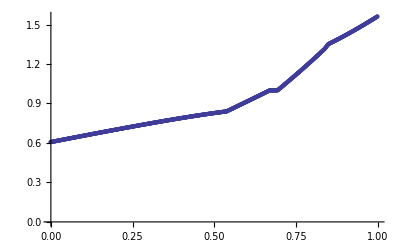

```mathematica
p3=ListPlot[tabT3]
```

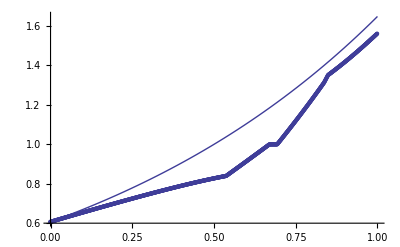

```mathematica
Show[pd1,p3]
```

### alfa = 8/10, t=1

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\agata.chmielowska\Desktop\AlgorytmC- — kopia

```mathematica
str4=OpenRead["temperatury.csv"]
```

InputStream[temperatury.csv,98]

```mathematica
strList4=ReadList[str4]
```

{2.71201,2.70963,2.70726,2.70489,2.70252,2.70016,2.69779,2.69543,2.69308,2.69072,2.68837,2.68602,2.68367,2.68133,2.67899,2.67665,2.67431,2.67198,2.66965,2.66732,2.66499,2.66267,2.66035,2.65803,2.65571,2.6534,2.65109,2.64878,2.64647,2.64417,2.64187,2.63957,2.63728,2.63499,2.6327,2.63041,2.62812,2.62584,2.62356,2.62129,2.61901,2.61674,2.61447,2.61221,2.60994,2.60768,2.60543,2.60317,2.60092,2.59867,2.59642,2.59417,2.59193,2.58969,2.58745,2.58522,2.58299,2.58076,2.57853,2.57631,2.57408,2.57186,2.56965,2.56743,2.56522,2.56301,2.56081,2.5586,2.5564,2.5542,2.55201,2.54981,2.54762,2.54543,2.54325,2.54106,2.53888,2.5367,2.53453,2.53235,2.53018,2.52801,2.52585,2.52368,2.52152,2.51937,2.51721,2.51506,2.51291,2.51076,2.50861,2.50647,2.50433,2.50219,2.50005,2.49792,2.49579,2.49366,2.49153,2.48941,2.48729,2.48517,2.48306,2.48094,2.47883,2.47672,2.47462,2.47251,2.47041,2.46831,2.46622,2.46413,2.46203,2.45995,2.45786,2.45578,2.45369,2.45162,2.44954,2.44746,2.44539,2.44332,2.44126,2.43919,2.43713,2.43507,2.43302,2.43096,2.42891,2.42686,2.42481,2.42277,2.42073,2.41869,2.41665,2.41461,2.41258,2.41055,2.40852,2.4065,2.40447,2.40245,2.40044,2.39842,2.39641,2.3944,2.39239,2.39038,2.38838,2.38638,2.38438,2.38238,2.38039,2.37839,2.37641,2.37442,2.37243,2.37045,2.36847,2.36649,2.36452,2.36255,2.36058,2.35861,2.35664,2.35468,2.35272,2.35076,2.3488,2.34685,2.3449,2.34295,2.341,2.33906,2.33712,2.33518,2.33324,2.33131,2.32937,2.32744,2.32552,2.32359,2.32167,2.31975,2.31783,2.31591,2.314,2.31209,2.31018,2.30828,2.30637,2.30447,2.30257,2.30068,2.29878,2.29689,2.295,2.29312,2.29123,2.28935,2.28747,2.28559,2.28372,2.28185,2.27998,2.27811,2.27625,2.27438,2.27252,2.27066,2.26881,2.26696,2.26511,2.26326,2.26141,2.25957,2.25773,2.25589,2.25405,2.25222,2.25038,2.24855,2.24673,2.2449,2.24308,2.24126,2.23944,2.23763,2.23581,2.234,2.23219,2.23039,2.22859,2.22678,2.22498,2.22319,2.22139,2.2196,2.21781,2.21602,2.21424,2.21246,2.21068,2.2089,2.20712,2.20535,2.20358,2.20181,2.20004,2.19828,2.19652,2.19476,2.193,2.19125,2.18949,2.18774,2.18599,2.18425,2.18251,2.18076,2.17903,2.17729,2.17555,2.17382,2.17209,2.17037,2.16864,2.16692,2.1652,2.16348,2.16176,2.16005,2.15834,2.15663,2.15492,2.15322,2.15152,2.14982,2.14812,2.14642,2.14473,2.14304,2.14135,2.13966,2.13798,2.1363,2.13462,2.13294,2.13126,2.12959,2.12792,2.12625,2.12459,2.12292,2.12126,2.1196,2.11794,2.11629,2.11464,2.11299,2.11134,2.10969,2.10805,2.10641,2.10477,2.10313,2.1015,2.09986,2.09823,2.0966,2.09498,2.09335,2.09173,2.09011,2.0885,2.08688,2.08527,2.08366,2.08205,2.08045,2.07884,2.07724,2.07564,2.07404,2.07245,2.07086,2.06927,2.06768,2.06609,2.06451,2.06293,2.06135,2.05977,2.05819,2.05662,2.05505,2.05348,2.05192,2.05035,2.04879,2.04723,2.04568,2.04412,2.04257,2.04102,2.03947,2.03793,2.03639,2.03484,2.03331,2.03177,2.03024,2.0287,2.02717,2.02565,2.02412,2.0226,2.02108,2.01956,2.01804,2.01653,2.01502,2.01351,2.012,2.0105,2.00899,2.00749,2.00599,2.0045,2.003,2.00151,2.00002,1.99854,1.99705,1.99557,1.99409,1.99261,1.99113,1.98966,1.98819,1.98672,1.98525,1.98379,1.98232,1.98086,1.9794,1.97795,1.97649,1.97504,1.97359,1.97214,1.9707,1.96926,1.96782,1.96638,1.96494,1.96351,1.96207,1.96064,1.95922,1.95779,1.95637,1.95495,1.95353,1.95211,1.9507,1.94928,1.94787,1.94647,1.94506,1.94366,1.94225,1.94085,1.93946,1.93806,1.93667,1.93528,1.93389,1.9325,1.93112,1.92974,1.92836,1.92698,1.92561,1.92423,1.92286,1.92149,1.92013,1.91876,1.9174,1.91604,1.91468,1.91332,1.91197,1.91062,1.90927,1.90792,1.90658,1.90523,1.90389,1.90255,1.90122,1.89988,1.89855,1.89722,1.89589,1.89456,1.89324,1.89192,1.8906,1.88928,1.88797,1.88665,1.88534,1.88403,1.88273,1.88142,1.88012,1.87882,1.87752,1.87623,1.87493,1.87364,1.87235,1.87106,1.86978,1.86849,1.86721,1.86593,1.86466,1.86338,1.86211,1.86084,1.85957,1.8583,1.85704,1.85578,1.85452,1.85326,1.85201,1.85075,1.8495,1.84826,1.84701,1.84576,1.84452,1.84328,1.84205,1.84081,1.83958,1.83835,1.83712,1.83589,1.83467,1.83344,1.83222,1.83101,1.82979,1.82858,1.82736,1.82616,1.82495,1.82374,1.82254,1.82134,1.82014,1.81895,1.81775,1.81656,1.81537,1.81418,1.813,1.81181,1.81063,1.80945,1.80828,1.8071,1.80593,1.80476,1.80359,1.80242,1.80126,1.8001,1.79894,1.79778,1.79663,1.79547,1.79432,1.79317,1.79203,1.79088,1.78974,1.7886,1.78746,1.78633,1.78519,1.78406,1.78293,1.7818,1.78068,1.77956,1.77844,1.77732,1.7762,1.77509,1.77397,1.77286,1.77176,1.77065,1.76955,1.76844,1.76734,1.76625,1.76515,1.76406,1.76297,1.76188,1.76079,1.75971,1.75863,1.75755,1.75647,1.75539,1.75432,1.75325,1.75218,1.75111,1.75004,1.74898,1.74792,1.74686,1.7458,1.74475,1.7437,1.74265,1.7416,1.74055,1.73951,1.73847,1.73743,1.73639,1.73535,1.73432,1.73329,1.73226,1.73123,1.73021,1.72918,1.72816,1.72714,1.72613,1.72511,1.7241,1.72309,1.72208,1.72108,1.72007,1.71907,1.71807,1.71707,1.71608,1.71509,1.71409,1.71311,1.71212,1.71113,1.71015,1.70917,1.70819,1.70722,1.70624,1.70527,1.7043,1.70333,1.70237,1.7014,1.70044,1.69948,1.69853,1.69757,1.69662,1.69567,1.69472,1.69377,1.69283,1.69189,1.69095,1.69001,1.68908,1.68814,1.68721,1.68628,1.68536,1.68443,1.68351,1.68259,1.68167,1.68076,1.67985,1.67893,1.67803,1.67712,1.67621,1.67531,1.67441,1.67351,1.67262,1.67172,1.67083,1.66994,1.66906,1.66817,1.66729,1.66641,1.66553,1.66465,1.66378,1.66291,1.66204,1.66117,1.66031,1.65944,1.65858,1.65772,1.65687,1.65601,1.65516,1.65431,1.65346,1.65262,1.65178,1.65093,1.6501,1.64926,1.64842,1.64759,1.64676,1.64593,1.64511,1.64428,1.64346,1.64264,1.64183,1.64101,1.6402,1.63939,1.63858,1.63777,1.63697,1.63617,1.63537,1.63457,1.63377,1.63298,1.63219,1.6314,1.63062,1.62983,1.62905,1.62827,1.62749,1.62672,1.62594,1.62517,1.6244,1.62363,1.62287,1.62211,1.62135,1.62059,1.61983,1.61908,1.61833,1.61758,1.61683,1.61609,1.61534,1.6146,1.61386,1.61313,1.61239,1.61166,1.61093,1.6102,1.60948,1.60875,1.60803,1.60731,1.6066,1.60588,1.60517,1.60446,1.60375,1.60305,1.60234,1.60164,1.60094,1.60024,1.59955,1.59886,1.59817,1.59748,1.59679,1.59611,1.59542,1.59475,1.59407,1.59339,1.59272,1.59205,1.59138,1.59071,1.59005,1.58939,1.58873,1.58807,1.58741,1.58676,1.58611,1.58546,1.58481,1.58417,1.58352,1.58288,1.58225,1.58161,1.58098,1.58035,1.57972,1.57909,1.57847,1.57784,1.57722,1.57661,1.57599,1.57538,1.57477,1.57416,1.57355,1.57295,1.57235,1.57175,1.57115,1.57056,1.56997,1.56938,1.56879,1.5682,1.56762,1.56704,1.56646,1.56589,1.56532,1.56475,1.56418,1.56361,1.56305,1.56249,1.56193,1.56138,1.56082,1.56027,1.55972,1.55918,1.55864,1.5581,1.55756,1.55702,1.55649,1.55596,1.55543,1.55491,1.55439,1.55387,1.55335,1.55283,1.55232,1.55181,1.55131,1.5508,1.5503,1.5498,1.5493,1.54881,1.54832,1.54783,1.54734,1.54686,1.54638,1.5459,1.54543,1.54496,1.54449,1.54402,1.54355,1.54309,1.54263,1.54218,1.54172,1.54127,1.54082,1.54038,1.53993,1.53949,1.53906,1.53862,1.53819,1.53776,1.53733,1.53691,1.53649,1.53607,1.53566,1.53524,1.53483,1.53443,1.53402,1.53362,1.53322,1.53283,1.53243,1.53204,1.53166,1.53127,1.53089,1.53051,1.53013,1.52976,1.52939,1.52902,1.52866,1.5283,1.52794,1.52758,1.52723,1.52688,1.52653,1.52619,1.52584,1.52551,1.52517,1.52484,1.52451,1.52418,1.52386,1.52354,1.52322,1.5229,1.52259,1.52228,1.52197,1.52167,1.52137,1.52107,1.52078,1.52049,1.5202,1.51991,1.51963,1.51935,1.51908,1.5188,1.51853,1.51827,1.518,1.51774,1.51748,1.51723,1.51698,1.51673,1.51648,1.51624,1.516,1.51576,1.51553,1.5153,1.51507,1.51485,1.51463,1.51441,1.51419,1.51398,1.51377,1.51357,1.51337,1.51317,1.51297,1.51278,1.51259,1.5124,1.51222,1.51204,1.51186,1.51169,1.51152,1.51135,1.51119,1.51103,1.51087,1.51072,1.51057,1.51042,1.51027,1.51013,1.51,1.50986,1.50973,1.5096,1.50948,1.50936,1.50924,1.50912,1.50901,1.5089,1.5088,1.5087,1.5086,1.5085,1.50841,1.50832,1.50824,1.50816,1.50808,1.508,1.50793,1.50786,1.5078,1.50774,1.50768,1.50763,1.50757,1.50753,1.50748,1.50744,1.50741,1.50737,1.50734,1.50731,1.50729,1.50727,1.50725,1.50724,1.50723,1.50722,1.50722,1.50722,1.50723,1.50724,1.50725,1.50726,1.50728,1.5073,1.50733,1.50736,1.50739,1.50742,1.50746,1.50751,1.50755,1.5076,1.50766}

```mathematica
strList3={2.7120103169,2.7096344153,2.7072611512,2.7048905221,2.7025225252,2.7001571581,2.6977944181,2.6954343025,2.6930768088,2.6907219343,2.6883696765,2.6860200328,2.6836730006,2.6813285772,2.6789867603,2.6766475481,2.6743109386,2.6719769301,2.6696455208,2.6673167087,2.6649904921,2.6626668691,2.6603458379,2.6580273967,2.6557115437,2.653398277,2.6510875949,2.6487794955,2.646473977,2.6441710376,2.6418707539,2.639573123,2.6372781421,2.6349858085,2.6326961192,2.6304090715,2.6281246626,2.6258428896,2.6235637499,2.6212872405,2.6190133587,2.6167421017,2.6144734667,2.612207451,2.6099440518,2.6076832662,2.6054250916,2.6031695251,2.600916564,2.5986662056,2.5964184471,2.5941732857,2.5919307186,2.5896907433,2.5874533568,2.5852185565,2.5829863396,2.5807567035,2.5785296453,2.5763051624,2.5740832524,2.5718639129,2.5696471418,2.5674329367,2.5652212953,2.5630122153,2.5608056946,2.5586017308,2.5564003216,2.5542014648,2.5520051582,2.5498113994,2.5476201862,2.5454315164,2.5432453877,2.5410617978,2.5388807446,2.5367022258,2.5345262392,2.5323527825,2.5301818535,2.5280134499,2.5258475696,2.5236842103,2.5215233699,2.519365046,2.5172092366,2.5150559393,2.5129051521,2.5107568726,2.5086110987,2.5064678282,2.504327059,2.5021887892,2.5000530168,2.4979197399,2.4957889566,2.4936606649,2.4915348628,2.4894115486,2.4872907201,2.4851723755,2.483056513,2.4809431305,2.4788322261,2.476723798,2.4746178442,2.4725143628,2.470413352,2.4683148098,2.4662187342,2.4641251235,2.4620339758,2.4599452891,2.4578590615,2.4557752912,2.4536939763,2.4516151149,2.4495387051,2.4474647451,2.445393233,2.4433241669,2.441257545,2.4391933654,2.4371316263,2.4350723257,2.4330154619,2.4309610329,2.428909037,2.4268594723,2.424812337,2.4227676291,2.420725347,2.4186854887,2.4166480524,2.4146130363,2.4125804386,2.4105502575,2.408522491,2.4064971375,2.4044741951,2.402453662,2.4004355363,2.3984198164,2.3964065003,2.3943955863,2.3923870726,2.3903809574,2.3883772389,2.3863759153,2.3843769848,2.3823804457,2.3803862966,2.3783945362,2.3764051634,2.3744181769,2.3724335755,2.370451358,2.3684715231,2.3664940697,2.3645189965,2.3625463024,2.3605759861,2.3586080464,2.3566424821,2.354679292,2.3527184748,2.3507600295,2.3488039547,2.3468502492,2.344898912,2.3429499416,2.3410033371,2.3390590971,2.3371172205,2.335177706,2.3332405526,2.331305759,2.329373324,2.3274433195,2.3255157435,2.3235905945,2.3216678704,2.3197475696,2.3178296903,2.3159142307,2.3140011891,2.3120905635,2.3101823524,2.3082765539,2.3063731662,2.3044721876,2.3025736164,2.3006774507,2.2987836889,2.2968923292,2.2950033698,2.2931168091,2.2912326452,2.2893508764,2.2874715011,2.2855945174,2.2837199237,2.2818477182,2.2799778992,2.2781104651,2.276245414,2.2743827443,2.2725224544,2.2706645423,2.2688090066,2.2669558455,2.2651050573,2.2632566402,2.2614105927,2.2595669131,2.2577255996,2.2558866506,2.2540500644,2.2522158394,2.2503839738,2.2485544661,2.2467273145,2.2449025175,2.2430800733,2.2412599803,2.2394422369,2.2376268413,2.2358137921,2.2340030875,2.2321947259,2.2303887057,2.2285850252,2.2267836829,2.2249846771,2.2231880061,2.2213936685,2.2196016625,2.2178119865,2.216024639,2.2142396184,2.212456923,2.2106765513,2.2088985016,2.2071227724,2.2053493621,2.2035782692,2.2018094919,2.2000430288,2.1982788783,2.1965170388,2.1947575088,2.1930002866,2.1912453708,2.1894927597,2.1877424519,2.1859944457,2.1842487397,2.1825053322,2.1807642218,2.1790254068,2.1772888858,2.1755546573,2.1738227196,2.1720930714,2.170365711,2.1686406369,2.1669178477,2.1651973418,2.1634791177,2.1617631738,2.1600495088,2.1583381211,2.1566290092,2.1549221716,2.1532176068,2.1515153134,2.1498152898,2.1481175345,2.1464220462,2.1447288233,2.1430378643,2.1413491678,2.1396627323,2.1379785564,2.1362966386,2.1346169774,2.1329395714,2.1312644192,2.1295915192,2.1279208701,2.1262524705,2.1245863188,2.1229224136,2.1212607536,2.1196013373,2.1179441632,2.11628923,2.1146365362,2.1129860804,2.1113378613,2.1096918773,2.1080481272,2.1064066094,2.1047673226,2.1031302654,2.1014954365,2.0998628343,2.098232458,2.0966043067,2.0949783797,2.0933546761,2.0917331953,2.0901139365,2.0884968988,2.0868820816,2.0852694841,2.0836591055,2.0820509451,2.0804450021,2.0788412759,2.0772397656,2.0756404705,2.0740433898,2.0724485227,2.0708558685,2.0692654264,2.0676771957,2.0660911755,2.0645073652,2.0629257639,2.0613464368,2.0597693825,2.0581945997,2.056622087,2.0550518431,2.0534838666,2.0519181561,2.0503547104,2.0487935281,2.0472346078,2.0456779483,2.0441235482,2.0425714062,2.0410215209,2.0394738912,2.0379285155,2.0363853927,2.0348445214,2.0333059004,2.0317695283,2.0302354039,2.0287035258,2.0271738927,2.0256465035,2.0241213567,2.0225984512,2.0210777857,2.0195593588,2.0180431693,2.016529216,2.0150174976,2.0135080129,2.0120007605,2.0104957393,2.008992948,2.0074923853,2.0059940501,2.004497941,2.0030040569,2.0015123966,2.0000229587,1.9985357421,1.9970507456,1.995567968,1.9940874079,1.9926090644,1.991132936,1.9896590217,1.9881873202,1.9867178304,1.985250551,1.983785481,1.9823226189,1.9808619639,1.9794035145,1.9779472697,1.9764932283,1.9750413891,1.973591751,1.9721443129,1.9706990734,1.9692560316,1.9678151863,1.9663765362,1.9649400804,1.9635058176,1.9620737466,1.9606438665,1.959216176,1.9577906741,1.9563673595,1.9549462312,1.9535272882,1.9521105291,1.9506959531,1.9492835589,1.9478733455,1.9464653117,1.9450594565,1.9436557789,1.9422542776,1.9408549516,1.9394577999,1.9380628213,1.9366700149,1.9352793794,1.933890914,1.9325046174,1.9311204887,1.9297385268,1.9283587307,1.9269810992,1.9256056314,1.9242323262,1.9228611826,1.9214921996,1.920125376,1.918760711,1.9173982034,1.9160378523,1.9146796566,1.9133236153,1.9119697275,1.9106179921,1.909268408,1.9079209744,1.9065756902,1.9052325544,1.9038915661,1.9025527242,1.9012160278,1.8998814759,1.8985490675,1.8972188017,1.8958906774,1.8945646938,1.8932408498,1.8919191446,1.8905995771,1.8892821469,1.8879668539,1.8866536976,1.8853426779,1.8840337945,1.8827270472,1.8814224356,1.8801199595,1.8788196187,1.8775214129,1.8762253419,1.8749314054,1.8736396032,1.872349935,1.8710624005,1.8697769995,1.8684937315,1.8672125962,1.8659335935,1.8646567229,1.8633819842,1.862109377,1.860838965,1.8595707475,1.8583047234,1.857040892,1.8557792523,1.8545198035,1.8532625447,1.8520074751,1.8507545938,1.8495039,1.8482553929,1.8470090715,1.8457649351,1.8445229828,1.8432832138,1.8420456273,1.8408102224,1.8395769983,1.8383459543,1.8371170894,1.835890403,1.8346658941,1.8334435621,1.8322234061,1.8310054252,1.8297896188,1.828575986,1.8273645261,1.8261552383,1.8249481218,1.8237431758,1.8225403996,1.8213397925,1.8201413536,1.8189450822,1.8177509775,1.8165590389,1.8153692655,1.8141816567,1.8129962117,1.8118129297,1.8106318101,1.8094528521,1.808276055,1.8071014181,1.8059289406,1.804758622,1.8035904613,1.8024244581,1.8012606115,1.8000989209,1.7989393855,1.7977820048,1.7966267779,1.7954737044,1.7943227833,1.7931740142,1.7920273963,1.7908829289,1.7897406115,1.7886004433,1.7874624238,1.7863265521,1.7851928278,1.7840612502,1.7829318186,1.7818045324,1.7806793909,1.7795563936,1.7784355399,1.7773168291,1.7762002605,1.7750858337,1.7739735479,1.7728634026,1.7717553972,1.7706495311,1.7695458037,1.7684442144,1.7673447627,1.7662474479,1.7651522694,1.7640592268,1.7629683194,1.7618795467,1.7607929081,1.7597084031,1.758626031,1.7575457915,1.7564676838,1.7553917075,1.7543178621,1.7532461469,1.7521765615,1.7511091054,1.750043778,1.7489805788,1.7479195073,1.7468605629,1.7458037453,1.7447490538,1.743696488,1.7426460474,1.7415977315,1.7405515397,1.7395074717,1.7384655269,1.7374257049,1.7363880052,1.7353524273,1.7343189708,1.7332876351,1.7322584199,1.7312313247,1.730206349,1.7291834924,1.7281627545,1.7271441348,1.7261276328,1.7251132482,1.7241009806,1.7230908296,1.7220827958,1.7210768797,1.7200730817,1.7190714023,1.718071842,1.7170744012,1.7160790805,1.7150858804,1.7140948012,1.7131058437,1.7121190081,1.7111342949,1.7101517042,1.7091712365,1.7081928919,1.7072166709,1.7062425735,1.7052706002,1.7043007512,1.7033330269,1.7023674275,1.7014039534,1.7004426048,1.699483382,1.6985263506,1.6975715103,1.6966188608,1.695668402,1.6947201336,1.6937740555,1.6928301674,1.6918884691,1.6909489605,1.6900116412,1.6890765112,1.6881435703,1.6872128182,1.6862842547,1.6853578797,1.6844336931,1.6835116945,1.682591884,1.6816742611,1.680758826,1.6798455782,1.6789345177,1.6780256444,1.677118958,1.6762144585,1.6753121456,1.6744120192,1.6735140791,1.6726183253,1.6717247576,1.6708333758,1.6699441798,1.6690571695,1.6681723447,1.6672897053,1.6664092512,1.6655309823,1.6646548983,1.6637809993,1.6629092851,1.6620397556,1.6611724106,1.6603072501,1.659444274,1.658583482,1.6577248742,1.6568684505,1.6560142107,1.6551621547,1.6543122824,1.6534645938,1.6526190888,1.6517757672,1.650934629,1.650095674,1.6492589023,1.6484243137,1.6475919081,1.6467616855,1.6459336458,1.6451077888,1.6442841146,1.6434626231,1.6426433141,1.6418261877,1.6410112437,1.6401984821,1.6393879029,1.6385795059,1.637773291,1.6369692584,1.6361674078,1.6353677392,1.6345702526,1.6337749479,1.632981825,1.632190884,1.6314021248,1.6306155472,1.6298311513,1.629048937,1.6282689043,1.6274910531,1.6267153834,1.6259418952,1.6251705883,1.6244014628,1.6236345186,1.6228697557,1.6221071741,1.6213467737,1.6205885544,1.6198325163,1.6190786593,1.6183269834,1.6175774885,1.6168301746,1.6160850418,1.6153420899,1.6146013189,1.6138627288,1.6131263196,1.6123920912,1.6116600437,1.6109301769,1.6102024909,1.6094769857,1.6087536612,1.6080325174,1.6073135543,1.6065967718,1.60588217,1.6051697488,1.6044595081,1.6037514481,1.6030455686,1.6023418696,1.6016403511,1.6009410131,1.6002438556,1.5995488786,1.598856082,1.5981654657,1.5974770299,1.5967907745,1.5961066994,1.5954248046,1.5947450902,1.594067556,1.5933922022,1.5927190286,1.5920480352,1.5913792221,1.5907125891,1.5900481363,1.5893858637,1.5887257712,1.5880678589,1.5874121266,1.5867585832,1.5861072384,1.5854581017,1.5848111829,1.5841664901,1.5835240288,1.5828838045,1.5822458229,1.5816100893,1.5809766094,1.5803453886,1.5797164324,1.5790897464,1.5784653361,1.577843207,1.5772233646,1.5766058143,1.5759905617,1.5753776123,1.5747669716,1.5741586449,1.5735526379,1.572948956,1.5723476047,1.5717485894,1.5711519156,1.5705575889,1.5699656146,1.5693759982,1.5687887452,1.568203861,1.5676213512,1.5670412211,1.5664634762,1.5658881956,1.5653153844,1.5647450475,1.56417719,1.563611817,1.5630489334,1.5624885443,1.5619306547,1.5613752696,1.5608223941,1.5602720332,1.5597241919,1.5591788752,1.5586360882,1.5580958359,1.5575581233,1.5570229555,1.5564903375,1.5559602743,1.5554327709,1.5549078324,1.5543854638,1.5538656702,1.5533484565,1.5528338278,1.5523217892,1.5518123456,1.5513055022,1.5508012639,1.5502996358,1.5498006229,1.5493042303,1.5488104631,1.5483193261,1.5478308246,1.5473449636,1.546861748,1.546381183,1.5459032736,1.5454280249,1.5449554419,1.5444855297,1.5440182933,1.5435537378,1.5430918683,1.5426326898,1.5421762074,1.5417224262,1.5412713512,1.5408229876,1.5403773404,1.5399344146,1.5394942155,1.5390567479,1.5386220171,1.5381900282,1.5377607862,1.5373342962,1.5369105634,1.5364895927,1.5360713895,1.5356559587,1.5352433054,1.5348334348,1.534426352,1.5340220622,1.5336205704,1.5332218818,1.5328260015,1.5324329346,1.5320426864,1.5316552619,1.5312706663,1.5308889047,1.5305099823,1.5301339043,1.5297606758,1.529390302,1.5290227881,1.5286581392,1.5282963605,1.5279374572,1.5275814346,1.5272282977,1.5268780519,1.5265307022,1.5261862539,1.5258447123,1.5255060825,1.5251703697,1.5248375793,1.5245077163,1.5241807862,1.523856794,1.5235357451,1.5232176447,1.522902498,1.5225903104,1.522281087,1.5219748333,1.5216715543,1.5213712556,1.5210739422,1.5207796195,1.5204882929,1.5201999676,1.519914649,1.5196323423,1.5193530529,1.5190767861,1.5188035473,1.5185333418,1.518266175,1.5180020521,1.5177409787,1.5174829599,1.5172280013,1.5169761082,1.516727286,1.5164815401,1.5162388758,1.5159992987,1.515762814,1.5155294273,1.5152991439,1.5150719694,1.514847909,1.5146269684,1.5144091529,1.514194468,1.5139829192,1.513774512,1.5135692518,1.5133671441,1.5131681945,1.5129724084,1.5127797914,1.512590349,1.5124040867,1.5122210101,1.5120411246,1.511864436,1.5116909496,1.5115206712,1.5113536062,1.5111897602,1.511029139,1.510871748,1.5107175928,1.5105666792,1.5104190127,1.5102745989,1.5101334436,1.5099955522,1.5098609307,1.5097295845,1.5096015193,1.509476741,1.5093552551,1.5092370673,1.5091221834,1.5090106092,1.5089023503,1.5087974124,1.5086958014,1.508597523,1.508502583,1.5084109871,1.5083227411,1.5082378509,1.5081563222,1.5080781609,1.5080033728,1.5079319637,1.5078639395,1.5077993061,1.5077380692,1.5076802348,1.5076258088,1.5075747971,1.5075272055,1.50748304,1.5074423066,1.5074050111,1.5073711595,1.5073407578,1.5073138102,1.5072903199,1.5072702902,1.5072537247,1.5072406266,1.5072309994,1.5072248464,1.5072221711,1.507222977,1.5072272674,1.507235046,1.5072463161,1.5072610814,1.5072793452,1.5073011113,1.5073263831,1.5073551643,1.5073874584,1.5074232691,1.5074625999,1.5075054547,1.5075518369,1.5076017504,1.5076551988};
```

```mathematica
tabT4=Table[{1-i*0.001,strList4[[i]]},{i,1,1001}];
```

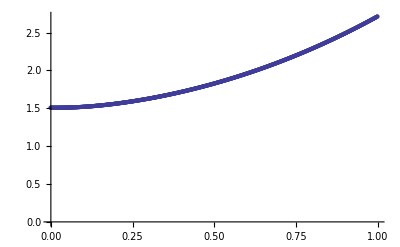

```mathematica
p4=ListPlot[tabT4]
```

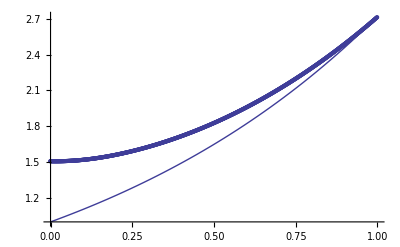

```mathematica
Show[pd2,p4]
```